```mathematica
ElastoPlasticB[epsp_,EP_,ETotal_]:=Block[{epspnext,θnext,EPnext,valf2,SigI1xJ2,EElast,EElastIJ,delepsp,I1next,J2next,lval,diffsig,diffsigIJ,sigresult,IJQuadrant,pr},
pr=True;
epspnext=epsp;
EElast=ETotal-EP;
EElastIJ=ToIJ[EElast];
IJQuadrant=EElastIJ[[3]];
SigI1xJ2={3K EElastIJ[[1]],2G EElastIJ[[2]],IJQuadrant}/.exemple;
valf2=Function2[SigI1xJ2[[1]],SigI1xJ2[[2]],epsp]//Chop;
If[pr,
Print["ETotal = ",ETotal];
Print["SigI1xJ2 = ",SigI1xJ2];
Print["valf2 = ",valf2]
];
If[valf2<= 0,
epspnext = epsp;
sigresult=FromIJ[SigI1xJ2];
EPnext=EP
,
{θnext,delepsp}=NewtonFunc2[epsp,SigI1xJ2];
epspnext=epsp+delepsp;
lval=LFunction[epspnext];
I1next=lval+F[lval]R Cos[θnext]/.exemple;
J2next=F[lval]Sin[θnext]/.exemple;
Print["Function2 = ",Function2[I1next,J2next,epspnext]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-FromIJ[{I1next,J2next,IJQuadrant}];
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
];
{epspnext,EPnext,sigresult,FromIJ[SigI1xJ2]}
]
locepsp=0;
EP={0,0};
ETotal={0.0001,0.0};
ElastoPlasticB[locepsp,EP,ETotal]
ETotal={-0.065/50,0.0};
ElastoPlasticB[locepsp,EP,ETotal]
```

ETotal = {0.0001,0.}

SigI1xJ2 = {0.02,0.0046188,-1}

valf2 = -0.27052

{0,{0,0},{0.012,0.004},{0.012,0.004}}

ETotal = {-0.0013,0.}

SigI1xJ2 = {-0.26,0.0600444,1}

valf2 = 9.00047

residue = {0.00624962,-0.000353992}

residue = {-1.17728×10^-6,6.27445×10^-7}

residue = {1.19016×10^-13,1.44884×10^-14}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

Function2 = 1.11022×10^-16

{-0.00127444,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}}

```mathematica
ListETotalB=Table[{epsa,0},{epsa,0,-0.065(1+1/50),-0.065/50}]
ListETotalB=Join[ListETotalB,Reverse[ListETotalB]]
ResultB={{0,{0,0},{0,0},{0,0}}};
ResultB[[-1,1]]
ResultB[[-1,2]]
test=ElastoPlasticB[ResultB[[-1,1]],ResultB[[-1,2]],ListETotalB[[2]]]
ElastoPlasticB[test[[1]],test[[2]],ListETotalB[[2]]]

For[i=2,i<=Length[ListETotalB],i++,
AppendTo[ResultB,ElastoPlasticB[ResultB[[-1,1]],ResultB[[-1,2]],ListETotalB[[i]]]]
]
ElastoPlasticB[ResultB[[-1,1]],ResultB[[-1,2]],ListETotalB[[-1]]]
```

{{0.,0},{-0.0013,0},{-0.0026,0},{-0.0039,0},{-0.0052,0},{-0.0065,0},{-0.0078,0},{-0.0091,0},{-0.0104,0},{-0.0117,0},{-0.013,0},{-0.0143,0},{-0.0156,0},{-0.0169,0},{-0.0182,0},{-0.0195,0},{-0.0208,0},{-0.0221,0},{-0.0234,0},{-0.0247,0},{-0.026,0},{-0.0273,0},{-0.0286,0},{-0.0299,0},{-0.0312,0},{-0.0325,0},{-0.0338,0},{-0.0351,0},{-0.0364,0},{-0.0377,0},{-0.039,0},{-0.0403,0},{-0.0416,0},{-0.0429,0},{-0.0442,0},{-0.0455,0},{-0.0468,0},{-0.0481,0},{-0.0494,0},{-0.0507,0},{-0.052,0},{-0.0533,0},{-0.0546,0},{-0.0559,0},{-0.0572,0},{-0.0585,0},{-0.0598,0},{-0.0611,0},{-0.0624,0},{-0.0637,0},{-0.065,0},{-0.0663,0}}

{{0.,0},{-0.0013,0},{-0.0026,0},{-0.0039,0},{-0.0052,0},{-0.0065,0},{-0.0078,0},{-0.0091,0},{-0.0104,0},{-0.0117,0},{-0.013,0},{-0.0143,0},{-0.0156,0},{-0.0169,0},{-0.0182,0},{-0.0195,0},{-0.0208,0},{-0.0221,0},{-0.0234,0},{-0.0247,0},{-0.026,0},{-0.0273,0},{-0.0286,0},{-0.0299,0},{-0.0312,0},{-0.0325,0},{-0.0338,0},{-0.0351,0},{-0.0364,0},{-0.0377,0},{-0.039,0},{-0.0403,0},{-0.0416,0},{-0.0429,0},{-0.0442,0},{-0.0455,0},{-0.0468,0},{-0.0481,0},{-0.0494,0},{-0.0507,0},{-0.052,0},{-0.0533,0},{-0.0546,0},{-0.0559,0},{-0.0572,0},{-0.0585,0},{-0.0598,0},{-0.0611,0},{-0.0624,0},{-0.0637,0},{-0.065,0},{-0.0663,0},{-0.0663,0},{-0.065,0},{-0.0637,0},{-0.0624,0},{-0.0611,0},{-0.0598,0},{-0.0585,0},{-0.0572,0},{-0.0559,0},{-0.0546,0},{-0.0533,0},{-0.052,0},{-0.0507,0},{-0.0494,0},{-0.0481,0},{-0.0468,0},{-0.0455,0},{-0.0442,0},{-0.0429,0},{-0.0416,0},{-0.0403,0},{-0.039,0},{-0.0377,0},{-0.0364,0},{-0.0351,0},{-0.0338,0},{-0.0325,0},{-0.0312,0},{-0.0299,0},{-0.0286,0},{-0.0273,0},{-0.026,0},{-0.0247,0},{-0.0234,0},{-0.0221,0},{-0.0208,0},{-0.0195,0},{-0.0182,0},{-0.0169,0},{-0.0156,0},{-0.0143,0},{-0.013,0},{-0.0117,0},{-0.0104,0},{-0.0091,0},{-0.0078,0},{-0.0065,0},{-0.0052,0},{-0.0039,0},{-0.0026,0},{-0.0013,0},{0.,0}}

0

{0,0}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.26,0.0600444,1}

valf2 = 9.00047

residue = {0.00624962,-0.000353992}

residue = {-1.17728×10^-6,6.27445×10^-7}

residue = {1.19016×10^-13,1.44884×10^-14}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

Function2 = 1.11022×10^-16

{-0.00127444,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.00511106,0.0313752,1}

valf2 = 0

{-0.00127444,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.0379327,0.0164108}}

ETotal = {-0.0013,0}

SigI1xJ2 = {-0.26,0.0600444,1}

valf2 = 9.00047

residue = {0.00624962,-0.000353992}

residue = {-1.17728×10^-6,6.27445×10^-7}

residue = {1.19016×10^-13,1.44884×10^-14}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

Function2 = 1.11022×10^-16

ETotal = {-0.0026,0}

SigI1xJ2 = {-0.265111,0.0914197,1}

valf2 = 8.85592

residue = {-0.00103468,0.000155634}

residue = {2.41752×10^-10,1.84871×10^-8}

residue = {4.44089×10^-16,-1.11022×10^-16}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

Function2 = 1.66533×10^-16

ETotal = {-0.0039,0}

SigI1xJ2 = {-0.269781,0.103975,1}

valf2 = 8.01407

residue = {0.00299513,-0.000342136}

residue = {-2.62616×10^-8,1.63072×10^-7}

residue = {1.33227×10^-15,-1.66533×10^-16}

residue = {0.,5.55112×10^-17}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0052,0}

SigI1xJ2 = {-0.285767,0.109549,1}

valf2 = 7.34999

residue = {0.00142855,-0.000157998}

residue = {-8.00416×10^-9,3.74444×10^-8}

residue = {0.,1.66533×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -2.77556×10^-16

ETotal = {-0.0065,0}

SigI1xJ2 = {-0.307798,0.112914,1}

valf2 = 6.83621

residue = {0.000951181,-0.0000757465}

residue = {-8.97987×10^-9,1.72797×10^-8}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0078,0}

SigI1xJ2 = {-0.332426,0.115576,1}

valf2 = 6.40586

residue = {0.000789069,-0.0000440498}

residue = {-9.72387×10^-9,1.22914×10^-8}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«2 more identical outputs»

Function2 = 1.66533×10^-16

ETotal = {-0.0091,0}

SigI1xJ2 = {-0.358292,0.118013,1}

valf2 = 6.02799

residue = {0.000730875,-0.0000316183}

residue = {-1.07783×10^-8,1.07734×10^-8}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«2 more identical outputs»

Function2 = 2.77556×10^-16

ETotal = {-0.0104,0}

SigI1xJ2 = {-0.384923,0.120382,1}

valf2 = 5.68899

residue = {0.0007085,-0.0000261381}

residue = {-1.20989×10^-8,1.02729×10^-8}

residue = {8.88178×10^-16,-1.66533×10^-16}

residue = {0.,-5.55112×10^-17}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2 = -1.66533×10^-16

ETotal = {-0.0117,0}

SigI1xJ2 = {-0.412164,0.122739,1}

valf2 = 5.38174

residue = {0.000698392,-0.000023093}

residue = {-1.35585×10^-8,1.00958×10^-8}

residue = {4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,-1.11022×10^-16}

residue = {4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,-1.11022×10^-16}

residue = {4.44089×10^-16,1.11022×10^-16}

Function2 = 1.66533×10^-16

ETotal = {-0.013,0}

SigI1xJ2 = {-0.43997,0.125103,1}

valf2 = 5.10164

residue = {0.000692025,-0.0000208257}

residue = {-1.50639×10^-8,1.00093×10^-8}

residue = {4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = -2.22045×10^-16

ETotal = {-0.0143,0}

SigI1xJ2 = {-0.468338,0.127481,1}

valf2 = 4.84523

residue = {0.000686155,-0.0000187092}

residue = {-1.65525×10^-8,9.9268×10^-9}

residue = {4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = -3.88578×10^-16

ETotal = {-0.0156,0}

SigI1xJ2 = {-0.497281,0.129876,1}

valf2 = 4.60973

residue = {0.00067944,-0.0000164913}

residue = {-1.79773×10^-8,9.81335×10^-9}

residue = {4.44089×10^-16,-1.66533×10^-16}

residue = {-4.44089×10^-16,1.66533×10^-16}

residue = {4.44089×10^-16,-1.66533×10^-16}

residue = {-4.44089×10^-16,1.66533×10^-16}

residue = {4.44089×10^-16,-1.66533×10^-16}

Function2 = -5.55112×10^-17

ETotal = {-0.0169,0}

SigI1xJ2 = {-0.526815,0.13229,1}

valf2 = 4.39279

residue = {0.000671236,-0.0000140564}

residue = {-1.92982×10^-8,9.65273×10^-9}

residue = {4.44089×10^-16,-1.11022×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 1.11022×10^-16

ETotal = {-0.0182,0}

SigI1xJ2 = {-0.556961,0.134722,1}

valf2 = 4.19242

residue = {0.000661151,-0.0000113392}

residue = {-2.04763×10^-8,9.43598×10^-9}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = -2.22045×10^-16

ETotal = {-0.0195,0}

SigI1xJ2 = {-0.587742,0.137174,1}

valf2 = 4.00689

residue = {0.000648871,-8.29115×10^-6}

residue = {-2.14718×10^-8,9.15715×10^-9}

residue = {0.,1.11022×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -1.11022×10^-16

ETotal = {-0.0208,0}

SigI1xJ2 = {-0.619182,0.139646,1}

valf2 = 3.83469

residue = {0.000634098,-4.86756×10^-6}

residue = {-2.22431×10^-8,8.8117×10^-9}

residue = {0.,1.11022×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -5.55112×10^-17

ETotal = {-0.0221,0}

SigI1xJ2 = {-0.651306,0.142138,1}

valf2 = 3.67451

residue = {0.000616517,-1.02232×10^-6}

residue = {-2.27464×10^-8,8.39607×10^-9}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = 1.66533×10^-16

ETotal = {-0.0234,0}

SigI1xJ2 = {-0.684141,0.144651,1}

valf2 = 3.52521

residue = {0.000595786,3.29478×10^-6}

residue = {-2.29366×10^-8,7.90772×10^-9}

residue = {0.,1.11022×10^-16}

residue = {0.,1.11022×10^-16}

residue = {0.,-1.11022×10^-16}

residue = {0.,1.11022×10^-16}

residue = {0.,-1.11022×10^-16}

Function2 = 0.

ETotal = {-0.0247,0}

SigI1xJ2 = {-0.717716,0.147184,1}

valf2 = 3.38577

residue = {0.000571524,8.13955×10^-6}

residue = {-2.27683×10^-8,7.34537×10^-9}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,1.11022×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = -1.11022×10^-16

ETotal = {-0.026,0}

SigI1xJ2 = {-0.752061,0.149739,1}

valf2 = 3.25529

residue = {0.000543303,0.0000135746}

residue = {-2.21979×10^-8,6.70954×10^-9}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,-1.11022×10^-16}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0273,0}

SigI1xJ2 = {-0.787207,0.152316,1}

valf2 = 3.13299

residue = {0.000510647,0.0000196705}

residue = {-2.11865×10^-8,6.00312×10^-9}

residue = {4.44089×10^-16,-3.33067×10^-16}

residue = {0.,2.22045×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {0.,2.22045×10^-16}

residue = {4.44089×10^-16,-3.33067×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0286,0}

SigI1xJ2 = {-0.823188,0.154915,1}

valf2 = 3.01815

residue = {0.000473016,0.0000265069}

residue = {-1.97038×10^-8,5.2323×10^-9}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {0.,-2.22045×10^-16}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {0.,-2.22045×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0299,0}

SigI1xJ2 = {-0.86004,0.157536,1}

valf2 = 2.91015

residue = {0.000429807,0.0000341738}

residue = {-1.77341×10^-8,4.40761×10^-9}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = -5.55112×10^-17

ETotal = {-0.0312,0}

SigI1xJ2 = {-0.8978,0.16018,1}

valf2 = 2.80843

residue = {0.000380336,0.0000427733}

residue = {-1.52842×10^-8,3.54547×10^-9}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0325,0}

SigI1xJ2 = {-0.936509,0.162848,1}

valf2 = 2.71248

residue = {0.000323835,0.0000524215}

residue = {-1.2394×10^-8,2.66996×10^-9}

residue = {4.44089×10^-16,-3.33067×10^-16}

residue = {-4.44089×10^-16,5.55112×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0338,0}

SigI1xJ2 = {-0.976209,0.165539,1}

valf2 = 2.62184

residue = {0.000259435,0.0000632499}

residue = {-9.15143×10^-9,1.81526×10^-9}

residue = {0.,-1.11022×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {0.,-3.33067×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {0.,-3.33067×10^-16}

Function2 = -1.11022×10^-16

ETotal = {-0.0351,0}

SigI1xJ2 = {-1.01694,0.168255,1}

valf2 = 2.53612

residue = {0.000186152,0.0000754087}

residue = {-5.71181×10^-9,1.02873×10^-9}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = 1.66533×10^-16

ETotal = {-0.0364,0}

SigI1xJ2 = {-1.05876,0.170996,1}

valf2 = 2.45493

residue = {0.000102876,0.0000890689}

residue = {-2.32445×10^-9,3.74863×10^-10}

residue = {8.88178×10^-16,-2.22045×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,2.22045×10^-16}

Function2 = -1.11022×10^-16

ETotal = {-0.0377,0}

SigI1xJ2 = {-1.10172,0.173762,1}

valf2 = 2.37795

residue = {8.34556×10^-6,0.000104426}

residue = {6.32324×10^-10,-5.96618×10^-11}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,-2.22045×10^-16}

Function2 = -1.66533×10^-16

ETotal = {-0.039,0}

SigI1xJ2 = {-1.14586,0.176553,1}

valf2 = 2.30487

residue = {-0.0000988685,0.000121703}

residue = {2.60433×10^-9,-1.59465×10^-10}

residue = {0.,-2.22045×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -1.66533×10^-16

ETotal = {-0.0403,0}

SigI1xJ2 = {-1.19126,0.179371,1}

valf2 = 2.23542

residue = {-0.00022039,0.000141158}

residue = {2.79951×10^-9,2.27857×10^-10}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«2 more identical outputs»

Function2 = 0.

ETotal = {-0.0416,0}

SigI1xJ2 = {-1.23796,0.182216,1}

valf2 = 2.16934

residue = {-0.000358065,0.000163084}

residue = {1.05794×10^-10,1.3024×10^-9}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,0.}

Function2 = -4.996×10^-16

ETotal = {-0.0429,0}

SigI1xJ2 = {-1.28603,0.185088,1}

valf2 = 2.1064

residue = {-0.000513996,0.000187819}

residue = {-7.01737×10^-9,3.32565×10^-9}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«2 more identical outputs»

Function2 = 2.22045×10^-16

ETotal = {-0.0442,0}

SigI1xJ2 = {-1.33556,0.187988,1}

valf2 = 2.0464

residue = {-0.000690578,0.000215755}

residue = {-2.06822×10^-8,6.63799×10^-9}

residue = {-8.88178×10^-16,4.44089×10^-16}

residue = {1.33227×10^-15,-4.44089×10^-16}

residue = {-8.88178×10^-16,4.44089×10^-16}

residue = {1.33227×10^-15,-4.44089×10^-16}

residue = {-8.88178×10^-16,4.44089×10^-16}

Function2 = -1.11022×10^-16

ETotal = {-0.0455,0}

SigI1xJ2 = {-1.3866,0.190917,1}

valf2 = 1.98914

residue = {-0.000890543,0.000247342}

residue = {-4.37608×10^-8,1.16811×10^-8}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

Function2 = -2.22045×10^-16

ETotal = {-0.0468,0}

SigI1xJ2 = {-1.43925,0.193875,1}

valf2 = 1.93445

residue = {-0.00111701,0.000283101}

residue = {-8.01332×10^-8,1.9027×10^-8}

residue = {-8.88178×10^-16,2.22045×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 1.11022×10^-16

ETotal = {-0.0481,0}

SigI1xJ2 = {-1.49358,0.196863,1}

valf2 = 1.88215

residue = {-0.00137356,0.000323637}

residue = {-1.35012×10^-7,2.94143×10^-8}

residue = {-1.33227×10^-15,4.44089×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

«1 more identical outputs»

Function2 = 5.55112×10^-17

ETotal = {-0.0494,0}

SigI1xJ2 = {-1.5497,0.199881,1}

valf2 = 1.8321

residue = {-0.00166427,0.000369649}

residue = {-2.15369×10^-7,4.37961×10^-8}

residue = {-3.55271×10^-15,8.88178×10^-16}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {8.88178×10^-16,0.}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,-2.22045×10^-16}

Function2 = 3.33067×10^-16

ETotal = {-0.0507,0}

SigI1xJ2 = {-1.6077,0.202931,1}

valf2 = 1.78415

residue = {-0.00199382,0.000421954}

residue = {-3.30492×10^-7,6.33997×10^-8}

residue = {-1.06581×10^-14,1.9984×10^-15}

residue = {8.88178×10^-16,0.}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {8.88178×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.052,0}

SigI1xJ2 = {-1.66768,0.206012,1}

valf2 = 1.73819

residue = {-0.00236758,0.000481501}

residue = {-4.92711×10^-7,8.98039×10^-8}

residue = {-2.22045×10^-14,3.33067×10^-15}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,2.22045×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0533,0}

SigI1xJ2 = {-1.72977,0.209125,1}

valf2 = 1.69408

residue = {-0.0027917,0.000549398}

residue = {-7.1834×10^-7,1.25038×10^-7}

residue = {-5.15143×10^-14,8.43769×10^-15}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0546,0}

SigI1xJ2 = {-1.79408,0.212272,1}

valf2 = 1.65171

residue = {-0.00327327,0.000626937}

residue = {-1.02891×10^-6,1.71705×10^-7}

residue = {-1.11022×10^-13,1.77636×10^-14}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -2.22045×10^-16

ETotal = {-0.0559,0}

SigI1xJ2 = {-1.86074,0.215452,1}

valf2 = 1.61099

residue = {-0.00382042,0.000715635}

residue = {-1.45274×10^-6,2.33145×10^-7}

residue = {-2.32703×10^-13,3.57492×10^-14}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {4.44089×10^-16,-6.66134×10^-16}

residue = {-4.44089×10^-16,6.66134×10^-16}

residue = {4.44089×10^-16,-6.66134×10^-16}

Function2 = -1.38778×10^-16

ETotal = {-0.0572,0}

SigI1xJ2 = {-1.92991,0.218667,1}

valf2 = 1.57179

residue = {-0.00444249,0.000817262}

residue = {-2.02695×10^-6,3.13633×10^-7}

residue = {-4.72067×10^-13,6.9722×10^-14}

residue = {1.33227×10^-15,-8.88178×10^-16}

residue = {-1.33227×10^-15,6.66134×10^-16}

residue = {1.33227×10^-15,-6.66134×10^-16}

residue = {-1.33227×10^-15,6.66134×10^-16}

Function2 = -2.498×10^-16

ETotal = {-0.0585,0}

SigI1xJ2 = {-2.00173,0.221916,1}

valf2 = 1.53404

residue = {-0.00515024,0.000933898}

residue = {-2.8001×10^-6,4.18639×10^-7}

residue = {-9.35696×10^-13,1.32783×10^-13}

residue = {-8.88178×10^-16,4.44089×10^-16}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = 2.77556×10^-16

ETotal = {-0.0598,0}

SigI1xJ2 = {-2.07636,0.2252,1}

valf2 = 1.49764

residue = {-0.00595606,0.00106798}

residue = {-3.83538×10^-6,5.55143×10^-7}

residue = {-1.8181×10^-12,2.49134×10^-13}

residue = {-1.77636×10^-15,4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,4.44089×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0611,0}

SigI1xJ2 = {-2.15398,0.228519,1}

valf2 = 1.46251

residue = {0.0286137,-0.00257158}

residue = {-0.000129098,0.0000156586}

residue = {-2.24464×10^-9,2.92391×10^-10}

residue = {0.,-4.44089×10^-16}

residue = {-1.77636×10^-15,8.88178×10^-16}

residue = {1.33227×10^-15,-8.88178×10^-16}

residue = {-1.77636×10^-15,8.88178×10^-16}

Function2 = -3.60822×10^-16

ETotal = {-0.0624,0}

SigI1xJ2 = {-2.23479,0.231873,1}

valf2 = 1.42856

residue = {0.0295233,-0.00276639}

residue = {-0.00013931,0.0000164739}

residue = {-2.68674×10^-9,3.39603×10^-10}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 1.38778×10^-16

ETotal = {-0.0637,0}

SigI1xJ2 = {-2.31897,0.235263,1}

valf2 = 1.39571

residue = {0.0305048,-0.00297121}

residue = {-0.000150636,0.000017374}

residue = {-3.22398×10^-9,3.95936×10^-10}

residue = {1.77636×10^-15,-8.88178×10^-16}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = -2.77556×10^-16

ETotal = {-0.065,0}

SigI1xJ2 = {-2.40675,0.238686,1}

valf2 = 1.36388

residue = {0.0315663,-0.00318542}

residue = {-0.000163252,0.0000183732}

residue = {-3.8797×10^-9,4.63565×10^-10}

residue = {-8.88178×10^-16,4.44089×10^-16}

residue = {4.44089×10^-16,4.44089×10^-16}

residue = {1.77636×10^-15,-1.33227×10^-15}

residue = {-2.22045×10^-15,8.88178×10^-16}

Function2 = -4.44089×10^-16

ETotal = {-0.0663,0}

SigI1xJ2 = {-2.49836,0.242142,1}

valf2 = 1.333

residue = {0.032716,-0.00340807}

residue = {-0.000177357,0.0000194871}

residue = {-4.68272×10^-9,5.45173×10^-10}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

residue = {4.44089×10^-16,0.}

«1 more identical outputs»

Function2 = 0.

ETotal = {-0.0663,0}

SigI1xJ2 = {-2.33404,0.185585,1}

valf2 = 0

ETotal = {-0.065,0}

SigI1xJ2 = {-2.07404,0.12554,1}

valf2 = -0.624624

ETotal = {-0.0637,0}

SigI1xJ2 = {-1.81404,0.0654958,1}

valf2 = -0.570878

ETotal = {-0.0624,0}

SigI1xJ2 = {-1.55404,0.00545141,1}

valf2 = 0.161238

Performing line search

listres = {{-0.612465,-0.0358611},{-0.52317,-0.0318951},{-0.41647,-0.0279409},{-0.289453,-0.0239987},{-0.140474,-0.0200683},{0.0290858,-0.0161498},{0.213137,-0.0122431},{0.401059,-0.00834828},{0.580845,-0.00446527},{0.743318,-0.000594087}}

normlistres = {0.613514,0.524142,0.417406,0.290447,0.141901,0.0332686,0.213488,0.401146,0.580862,0.743318}

ord = {6,5,7,4,8,3,2,9,1,10}

residue = {0.0290858,-0.0161498}

tangent = {{40.3236,-9.06509},{-0.0136618,312.467}}

delu = {0.000709698,-0.0000516538}

θ = 0.025831

delepsp = 0.000127944

resnormafter 0.00639222 resnormbefore 0.0332686

residue = {-0.0063922,-0.0000150123}

tangent = {{49.1636,-162.39},{-0.0132846,311.891}}

delu = {-0.000130196,-5.36786×10^-8}

θ = 0.0259612

delepsp = 0.000127998

resnormafter 2.21685×10^-6 resnormbefore 0.00639222

residue = {2.21684×10^-6,-4.37227×10^-9}

tangent = {{49.1858,-135.2},{-0.0133516,311.891}}

delu = {4.50376×10^-8,-1.20906×10^-11}

θ = 0.0259612

delepsp = 0.000127998

resnormafter 4.37409×10^-14 resnormbefore 2.21685×10^-6

residue = {-4.37358×10^-14,-6.66134×10^-16}

tangent = {{49.1858,-135.209},{-0.0133516,311.891}}

delu = {-8.95174×10^-16,-2.17411×10^-18}

θ = 0.0259612

delepsp = 0.000127998

resnormafter 1.10191×10^-15 resnormbefore 4.37409×10^-14

residue = {-8.7777×10^-16,6.66134×10^-16}

tangent = {{49.1858,-135.209},{-0.0133516,311.891}}

delu = {-1.19762×10^-17,2.13528×10^-18}

θ = 0.0259612

delepsp = 0.000127998

resnormafter 1.07448×10^-15 resnormbefore 1.10191×10^-15

residue = {8.43076×10^-16,-6.66134×10^-16}

tangent = {{49.1858,-135.209},{-0.0133516,311.891}}

delu = {1.12708×10^-17,-2.13531×10^-18}

θ = 0.0259612

delepsp = 0.000127998

resnormafter 1.10191×10^-15 resnormbefore 1.07448×10^-15

residue = {-8.7777×10^-16,6.66134×10^-16}

Function2 = 0.

ETotal = {-0.0611,0}

SigI1xJ2 = {-1.31964,0.0547038,-1}

valf2 = 1.3362

residue = {0.14351,-0.00637392}

residue = {-0.000341103,-0.0000907423}

residue = {6.0722×10^-8,-1.14124×10^-9}

residue = {1.249×10^-15,-8.88178×10^-16}

residue = {-8.04912×10^-16,6.66134×10^-16}

residue = {8.04912×10^-16,-6.66134×10^-16}

residue = {-8.04912×10^-16,6.66134×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0598,0}

SigI1xJ2 = {-1.238,0.107573,-1}

valf2 = 1.48878

residue = {-0.0531723,-0.00443885}

residue = {0.000896098,-0.0000264822}

residue = {1.38795×10^-7,-5.65636×10^-9}

residue = {2.33147×10^-15,2.22045×10^-16}

residue = {-3.33067×10^-16,2.22045×10^-16}

residue = {0.,0.}

residue = {0.,0.}

Function2 = -1.11022×10^-16

ETotal = {-0.0585,0}

SigI1xJ2 = {-1.17937,0.150493,-1}

valf2 = 1.56939

residue = {-0.0182701,-0.00440966}

residue = {0.000125279,-6.67527×10^-6}

residue = {3.05434×10^-9,-1.6719×10^-10}

residue = {-6.66134×10^-16,4.44089×10^-16}

residue = {-1.11022×10^-16,0.}

residue = {-1.11022×10^-16,0.}

residue = {-1.11022×10^-16,0.}

Function2 = 3.33067×10^-16

ETotal = {-0.0572,0}

SigI1xJ2 = {-1.13494,0.181856,-1}

valf2 = 1.59455

residue = {-0.0158141,-0.00385551}

residue = {0.000068884,-6.46649×10^-6}

residue = {8.14008×10^-10,-6.70601×10^-11}

residue = {1.33227×10^-15,-6.66134×10^-16}

residue = {-7.77156×10^-16,4.44089×10^-16}

residue = {1.22125×10^-15,-4.44089×10^-16}

residue = {-1.88738×10^-15,4.44089×10^-16}

Function2 = -6.10623×10^-16

ETotal = {-0.0559,0}

SigI1xJ2 = {-1.09459,0.201666,-1}

valf2 = 1.58837

residue = {-0.0155617,-0.00325839}

residue = {0.0000460538,-6.65589×10^-6}

residue = {2.95135×10^-10,-3.44886×10^-11}

residue = {-7.77156×10^-16,4.44089×10^-16}

residue = {-1.11022×10^-16,2.22045×10^-16}

residue = {-1.11022×10^-16,-2.22045×10^-16}

residue = {0.,0.}

Function2 = -1.11022×10^-16

ETotal = {-0.0546,0}

SigI1xJ2 = {-1.05038,0.212096,-1}

valf2 = 1.57669

residue = {-0.00590663,-0.00278792}

residue = {4.5943×10^-6,-1.47294×10^-6}

residue = {2.19447×10^-12,-3.45723×10^-13}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -1.11022×10^-16

ETotal = {-0.0533,0}

SigI1xJ2 = {-0.999643,0.216323,-1}

valf2 = 1.57545

residue = {-0.00171874,-0.00296756}

residue = {-3.47878×10^-7,-4.98843×10^-7}

residue = {-5.32907×10^-15,-1.57652×10^-14}

residue = {-8.88178×10^-16,4.44089×10^-16}

residue = {1.33227×10^-15,-5.55112×10^-16}

residue = {-1.33227×10^-15,4.44089×10^-16}

residue = {-4.44089×10^-16,3.33067×10^-16}

Function2 = -1.11022×10^-16

ETotal = {-0.052,0}

SigI1xJ2 = {-0.943767,0.21699,-1}

valf2 = 1.58849

residue = {0.000713282,-0.00309446}

residue = {-5.47865×10^-7,-2.70605×10^-7}

residue = {2.10942×10^-14,-1.18794×10^-14}

residue = {0.,-1.11022×10^-16}

residue = {0.,1.11022×10^-16}

residue = {0.,-1.11022×10^-16}

residue = {0.,1.11022×10^-16}

Function2 = 2.498×10^-16

ETotal = {-0.0507,0}

SigI1xJ2 = {-0.88527,0.215757,-1}

valf2 = 1.61346

residue = {0.00176814,-0.00306283}

residue = {-1.06282×10^-7,-2.33507×10^-7}

residue = {-2.88658×10^-15,-2.33147×10^-15}

residue = {8.88178×10^-16,-4.44089×10^-16}

residue = {-1.33227×10^-15,6.66134×10^-16}

residue = {1.33227×10^-15,-4.44089×10^-16}

residue = {-1.33227×10^-15,4.44089×10^-16}

Function2 = -5.55112×10^-17

ETotal = {-0.0494,0}

SigI1xJ2 = {-0.826231,0.213538,-1}

valf2 = 1.64687

residue = {0.00194522,-0.00291885}

residue = {8.57147×10^-8,-2.05231×10^-7}

residue = {-1.55431×10^-15,-7.77156×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {2.22045×10^-16,-1.11022×10^-16}

residue = {2.22045×10^-16,-1.11022×10^-16}

residue = {2.22045×10^-16,1.11022×10^-16}

Function2 = 1.11022×10^-16

ETotal = {-0.0481,0}

SigI1xJ2 = {-0.767966,0.210816,-1}

valf2 = 1.68609

residue = {0.00167197,-0.00271917}

residue = {6.83772×10^-8,-1.64801×10^-7}

residue = {6.66134×10^-16,-8.88178×10^-16}

residue = {-4.44089×10^-16,2.22045×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0468,0}

SigI1xJ2 = {-0.711194,0.207844,-1}

valf2 = 1.72946

residue = {0.00121444,-0.00250135}

residue = {-1.5636×10^-8,-1.25119×10^-7}

residue = {6.66134×10^-16,-7.77156×10^-16}

residue = {-1.33227×10^-15,4.44089×10^-16}

residue = {-4.44089×10^-16,1.11022×10^-16}

residue = {0.,0.}

residue = {0.,0.}

Function2 = -8.32667×10^-17

ETotal = {-0.0455,0}

SigI1xJ2 = {-0.656261,0.204757,-1}

valf2 = 1.77608

residue = {0.000713215,-0.00228565}

residue = {-9.02854×10^-8,-9.47461×10^-8}

residue = {0.,-4.44089×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 1.94289×10^-16

ETotal = {-0.0442,0}

SigI1xJ2 = {-0.603297,0.201624,-1}

valf2 = 1.8255

residue = {0.000234348,-0.00208164}

residue = {-1.33129×10^-7,-7.53357×10^-8}

residue = {8.88178×10^-16,-8.88178×10^-16}

residue = {2.22045×10^-16,0.}

residue = {2.22045×10^-16,0.}

residue = {2.22045×10^-16,-2.22045×10^-16}

residue = {-6.66134×10^-16,4.44089×10^-16}

Function2 = -5.55112×10^-17

ETotal = {-0.0429,0}

SigI1xJ2 = {-0.552319,0.198483,-1}

valf2 = 1.87756

residue = {-0.000195265,-0.00189306}

residue = {-1.45784×10^-7,-6.51889×10^-8}

residue = {-6.66134×10^-16,0.}

residue = {-2.22045×10^-16,0.}

residue = {-2.22045×10^-16,0.}

residue = {-2.22045×10^-16,0.}

residue = {-2.22045×10^-16,1.11022×10^-16}

Function2 = 2.77556×10^-17

ETotal = {-0.0416,0}

SigI1xJ2 = {-0.503282,0.195353,-1}

valf2 = 1.93224

residue = {-0.000567809,-0.00172074}

residue = {-1.36993×10^-7,-6.17395×10^-8}

residue = {4.44089×10^-16,-3.33067×10^-16}

residue = {-8.88178×10^-16,2.22045×10^-16}

residue = {2.22045×10^-16,0.}

residue = {8.88178×10^-16,-3.33067×10^-16}

residue = {-8.88178×10^-16,3.33067×10^-16}

Function2 = -2.77556×10^-17

ETotal = {-0.0403,0}

SigI1xJ2 = {-0.456115,0.192244,-1}

valf2 = 1.98962

residue = {-0.000884154,-0.00156413}

residue = {-1.15639×10^-7,-6.26262×10^-8}

residue = {4.44089×10^-16,-3.88578×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -1.38778×10^-16

ETotal = {-0.039,0}

SigI1xJ2 = {-0.410735,0.18916,-1}

valf2 = 2.04983

residue = {-0.00114874,-0.00142214}

residue = {-8.86214×10^-8,-6.60032×10^-8}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-1.11022×10^-15,3.33067×10^-16}

residue = {-2.22045×10^-16,1.11022×10^-16}

residue = {-2.22045×10^-16,0.}

residue = {4.44089×10^-16,0.}

Function2 = -1.66533×10^-16

ETotal = {-0.0377,0}

SigI1xJ2 = {-0.367055,0.186105,-1}

valf2 = 2.11306

residue = {-0.00136718,-0.00129349}

residue = {-6.06511×10^-8,-7.05424×10^-8}

residue = {2.22045×10^-16,-2.77556×10^-16}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

«1 more identical outputs»

Function2 = 5.55112×10^-17

ETotal = {-0.0364,0}

SigI1xJ2 = {-0.324988,0.183078,-1}

valf2 = 2.17951

residue = {-0.00154513,-0.00117689}

residue = {-3.46381×10^-8,-7.5341×10^-8}

residue = {-2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,5.55112×10^-17}

residue = {-2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,5.55112×10^-17}

residue = {-2.22045×10^-16,-5.55112×10^-17}

Function2 = -5.55112×10^-17

ETotal = {-0.0351,0}

SigI1xJ2 = {-0.284452,0.180082,-1}

valf2 = 2.24941

residue = {-0.00168791,-0.00107112}

residue = {-1.21757×10^-8,-7.98175×10^-8}

residue = {2.22045×10^-16,-2.77556×10^-16}

residue = {2.22045×10^-16,-1.11022×10^-16}

residue = {2.22045×10^-16,0.}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

Function2 = -5.55112×10^-17

ETotal = {-0.0338,0}

SigI1xJ2 = {-0.245369,0.177115,-1}

valf2 = 2.32303

residue = {-0.00180028,-0.000975086}

residue = {6.04313×10^-9,-8.3623×10^-8}

residue = {-4.44089×10^-16,0.}

residue = {2.22045×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {2.22045×10^-16,0.}

residue = {-4.44089×10^-16,0.}

Function2 = 5.55112×10^-17

ETotal = {-0.0325,0}

SigI1xJ2 = {-0.207665,0.174176,-1}

valf2 = 2.40065

residue = {-0.00188644,-0.000887786}

residue = {1.99087×10^-8,-8.65721×10^-8}

residue = {2.22045×10^-16,-1.11022×10^-16}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-6.66134×10^-16,2.77556×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {2.22045×10^-16,-5.55112×10^-17}

Function2 = -1.11022×10^-16

ETotal = {-0.0312,0}

SigI1xJ2 = {-0.171268,0.171267,-1}

valf2 = 2.48258

residue = {-0.00195008,-0.000808331}

residue = {2.96664×10^-8,-8.85914×10^-8}

residue = {-2.22045×10^-16,-2.77556×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,0.}

residue = {-2.22045×10^-16,2.77556×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

Function2 = 0.

ETotal = {-0.0299,0}

SigI1xJ2 = {-0.136115,0.168386,-1}

valf2 = 2.56919

residue = {-0.00199441,-0.000735929}

residue = {3.57597×10^-8,-8.96818×10^-8}

residue = {4.44089×10^-16,-2.22045×10^-16}

residue = {2.22045×10^-16,-2.77556×10^-17}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,2.77556×10^-17}

residue = {-2.22045×10^-16,0.}

Function2 = 0.

ETotal = {-0.0286,0}

SigI1xJ2 = {-0.102143,0.165532,-1}

valf2 = 2.66087

residue = {-0.00202219,-0.000669873}

residue = {3.87242×10^-8,-8.9892×10^-8}

residue = {-2.22045×10^-16,1.38778×10^-17}

residue = {2.22045×10^-16,-6.93889×10^-17}

residue = {2.22045×10^-16,-1.38778×10^-17}

residue = {-2.22045×10^-16,6.93889×10^-17}

residue = {-2.22045×10^-16,1.38778×10^-17}

Function2 = 1.66533×10^-16

ETotal = {-0.0273,0}

SigI1xJ2 = {-0.0692938,0.162706,-1}

valf2 = 2.75803

residue = {-0.00203586,-0.000609537}

residue = {3.91188×10^-8,-8.92991×10^-8}

residue = {2.22045×10^-16,-1.11022×10^-16}

residue = {2.22045×10^-16,-2.77556×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

Function2 = -5.55112×10^-17

ETotal = {-0.026,0}

SigI1xJ2 = {-0.0375139,0.159907,-1}

valf2 = 2.86118

residue = {-0.00203749,-0.000554361}

residue = {3.74835×10^-8,-8.79954×10^-8}

residue = {0.,-5.55112×10^-17}

residue = {0.,-2.77556×10^-17}

residue = {0.,2.77556×10^-17}

residue = {0.,-2.77556×10^-17}

residue = {0.,2.77556×10^-17}

Function2 = -5.55112×10^-17

ETotal = {-0.0247,0}

SigI1xJ2 = {-0.00675202,0.157134,-1}

valf2 = 2.97083

residue = {-0.00202889,-0.000503847}

residue = {3.43144×10^-8,-8.60789×10^-8}

residue = {2.22045×10^-16,-1.4138×10^-16}

residue = {2.22045×10^-16,-3.03577×10^-17}

residue = {0.,-2.60209×10^-18}

residue = {0.,-2.60209×10^-18}

residue = {0.,-2.60209×10^-18}

Function2 = 1.66533×10^-16

ETotal = {-0.0234,0}

SigI1xJ2 = {0.0230398,0.154386,-1}

valf2 = 3.0876

residue = {-0.00201165,-0.000457551}

residue = {3.0051×10^-8,-8.36479×10^-8}

residue = {6.66134×10^-16,-1.73472×10^-16}

residue = {-2.22045×10^-16,2.08167×10^-17}

residue = {0.,-3.46945×10^-17}

residue = {0.,2.08167×10^-17}

residue = {0.,2.08167×10^-17}

Function2 = -1.66533×10^-16

ETotal = {-0.0221,0}

SigI1xJ2 = {0.0519066,0.151664,-1}

valf2 = 3.21215

residue = {-0.00198711,-0.000415076}

residue = {2.50715×10^-8,-8.07962×10^-8}

residue = {6.66134×10^-16,-1.59595×10^-16}

residue = {-2.22045×10^-16,3.46945×10^-17}

residue = {2.22045×10^-16,-2.08167×10^-17}

residue = {-2.22045×10^-16,3.46945×10^-17}

residue = {2.22045×10^-16,-2.08167×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0208,0}

SigI1xJ2 = {0.0798909,0.148967,-1}

valf2 = 3.34524

residue = {-0.00195645,-0.000376067}

residue = {1.96929×10^-8,-7.76113×10^-8}

residue = {4.44089×10^-16,-1.52656×10^-16}

residue = {0.,1.38778×10^-17}

residue = {0.,1.38778×10^-17}

residue = {0.,1.38778×10^-17}

«1 more identical outputs»

Function2 = 1.11022×10^-16

ETotal = {-0.0195,0}

SigI1xJ2 = {0.107032,0.146294,-1}

valf2 = 3.48772

residue = {-0.0019207,-0.000340205}

residue = {1.41749×10^-8,-7.41727×10^-8}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-4.44089×10^-16,5.55112×10^-17}

residue = {2.22045×10^-16,0.}

residue = {-4.44089×10^-16,0.}

residue = {2.22045×10^-16,0.}

Function2 = 5.55112×10^-17

ETotal = {-0.0182,0}

SigI1xJ2 = {0.133369,0.143646,-1}

valf2 = 3.64056

residue = {-0.00188073,-0.000307205}

residue = {8.72443×10^-9,-7.05515×10^-8}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,-2.77556×10^-17}

residue = {-2.22045×10^-16,2.77556×10^-17}

residue = {2.22045×10^-16,-2.77556×10^-17}

residue = {-2.22045×10^-16,2.77556×10^-17}

Function2 = -5.55112×10^-17

ETotal = {-0.0169,0}

SigI1xJ2 = {0.158936,0.14102,-1}

valf2 = 3.80486

residue = {-0.00183732,-0.000276811}

residue = {3.50179×10^-9,-6.68105×10^-8}

residue = {6.66134×10^-16,-2.498×10^-16}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,2.77556×10^-17}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,2.77556×10^-17}

Function2 = -1.11022×10^-16

ETotal = {-0.0156,0}

SigI1xJ2 = {0.183766,0.138418,-1}

valf2 = 3.98185

residue = {-0.00179111,-0.000248793}

residue = {-1.37313×10^-9,-6.30041×10^-8}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,0.}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,0.}

residue = {-2.22045×10^-16,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.0143,0}

SigI1xJ2 = {0.207892,0.135839,-1}

valf2 = 4.17297

residue = {-0.00174268,-0.000222942}

residue = {-5.81509×10^-9,-5.91791×10^-8}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {4.44089×10^-16,-1.94289×10^-16}

residue = {-2.22045×10^-16,1.38778×10^-16}

residue = {2.22045×10^-16,2.77556×10^-17}

residue = {0.,-1.38778×10^-16}

Function2 = -5.55112×10^-17

ETotal = {-0.013,0}

SigI1xJ2 = {0.231343,0.133282,-1}

valf2 = 4.37987

residue = {-0.00169252,-0.000199072}

residue = {-9.76784×10^-9,-5.53751×10^-8}

residue = {0.,-5.55112×10^-17}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 2.22045×10^-16

ETotal = {-0.0117,0}

SigI1xJ2 = {0.254148,0.130747,-1}

valf2 = 4.60442

residue = {-0.00164106,-0.000177013}

residue = {-1.31992×10^-8,-5.16252×10^-8}

residue = {-2.22045×10^-16,1.11022×10^-16}

residue = {2.22045×10^-16,0.}

residue = {2.22045×10^-16,-2.22045×10^-16}

residue = {-2.22045×10^-16,1.11022×10^-16}

residue = {2.22045×10^-16,5.55112×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0104,0}

SigI1xJ2 = {0.276332,0.128233,-1}

valf2 = 4.84884

residue = {-0.00158867,-0.000156613}

residue = {-1.60963×10^-8,-4.79568×10^-8}

residue = {-4.44089×10^-16,1.66533×10^-16}

residue = {-2.22045×10^-16,0.}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0091,0}

SigI1xJ2 = {0.297922,0.125741,-1}

valf2 = 5.11566

residue = {-0.00153565,-0.000137734}

residue = {-1.84623×10^-8,-4.43922×10^-8}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,5.55112×10^-17}

residue = {-2.22045×10^-16,-5.55112×10^-17}

residue = {2.22045×10^-16,5.55112×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0078,0}

SigI1xJ2 = {0.31894,0.12327,-1}

valf2 = 5.40789

residue = {-0.00148229,-0.00012025}

residue = {-2.0312×10^-8,-4.0949×10^-8}

residue = {0.,-1.11022×10^-16}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 0.

ETotal = {-0.0065,0}

SigI1xJ2 = {0.339411,0.120818,-1}

valf2 = 5.72904

residue = {-0.0014288,-0.000104047}

residue = {-2.167×10^-8,-3.76409×10^-8}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,5.55112×10^-17}

Function2 = -2.22045×10^-16

ETotal = {-0.0052,0}

SigI1xJ2 = {0.359354,0.118388,-1}

valf2 = 6.08327

residue = {-0.00137539,-0.0000890227}

residue = {-2.25677×10^-8,-3.44784×10^-8}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {-2.22045×10^-16,1.11022×10^-16}

residue = {2.22045×10^-16,-1.66533×10^-16}

residue = {-2.22045×10^-16,1.66533×10^-16}

residue = {2.22045×10^-16,-1.66533×10^-16}

Function2 = 0.

ETotal = {-0.0039,0}

SigI1xJ2 = {0.378791,0.115976,-1}

valf2 = 6.47556

residue = {-0.00132223,-0.0000750827}

residue = {-2.30413×10^-8,-3.14687×10^-8}

residue = {0.,-5.55112×10^-17}

residue = {0.,-5.55112×10^-17}

residue = {0.,-5.55112×10^-17}

residue = {0.,5.55112×10^-17}

residue = {0.,-5.55112×10^-17}

Function2 = 5.55112×10^-17

ETotal = {-0.0026,0}

SigI1xJ2 = {0.39774,0.113585,-1}

valf2 = 6.91185

residue = {-0.00126945,-0.0000621414}

residue = {-2.31302×10^-8,-2.86168×10^-8}

residue = {-1.11022×10^-16,0.}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = -5.55112×10^-17

ETotal = {-0.0013,0}

SigI1xJ2 = {0.416221,0.111212,-1}

valf2 = 7.39934

residue = {-0.00121719,-0.000050121}

residue = {-2.28758×10^-8,-2.59253×10^-8}

residue = {3.33067×10^-16,-1.11022×10^-16}

residue = {0.,-5.55112×10^-17}

residue = {-2.22045×10^-16,1.11022×10^-16}

residue = {2.22045×10^-16,-5.55112×10^-17}

residue = {0.,-5.55112×10^-17}

Function2 = -3.33067×10^-16

ETotal = {0.,0}

SigI1xJ2 = {0.43425,0.108859,-1}

valf2 = 7.9468

residue = {-0.00116553,-0.0000389503}

residue = {-2.23202×10^-8,-2.33953×10^-8}

residue = {-1.11022×10^-16,5.55112×10^-17}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 2.77556×10^-16

ETotal = {0.,0}

SigI1xJ2 = {0.191845,0.046479,-1}

valf2 = 0

{-0.000959224,{-0.000990608,0.0000156919},{0.117618,0.0371136},{0.117618,0.0371136}}

```mathematica
ResultB
ResultIJ=Table[{ResultB[[i,1]],ToIJ[ResultB[[i,2]]],ToIJ[ResultB[[i,3]]],ToIJ[ResultB[[i,4]]]},{i,Length[ResultB]}]
```

{{0,{0,0},{0,0},{0,0}},{-0.00127444,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}},{-0.00255109,{-0.00194962,-0.000300736},{-0.0539865,0.0221027},{-0.193933,-0.0355892}},{-0.00377116,{-0.00314251,-0.000314325},{-0.0657524,0.0199926},{-0.209986,-0.0298973}},{-0.00496101,{-0.00435722,-0.000301893},{-0.0769818,0.0145918},{-0.221752,-0.0320074}},{-0.00613787,{-0.00557776,-0.000280056},{-0.0882645,0.00791936},{-0.232982,-0.0374082}},{-0.00730854,{-0.00679948,-0.000254529},{-0.0996999,0.000703864},{-0.244264,-0.0440806}},{-0.00847538,{-0.0080209,-0.000227244},{-0.111313,-0.00680515},{-0.2557,-0.0512961}},{-0.00963918,{-0.00924148,-0.000198853},{-0.123115,-0.0145244},{-0.267313,-0.0588051}},{-0.0108002,{-0.010461,-0.00016957},{-0.135113,-0.0224283},{-0.279115,-0.0665244}},{-0.0119583,{-0.0116794,-0.000139452},{-0.147315,-0.0305115},{-0.291113,-0.0744283}},{-0.0131136,{-0.0128966,-0.000108501},{-0.159729,-0.0387761},{-0.303315,-0.0825115}},{-0.0142659,{-0.0141125,-0.000076695},{-0.17236,-0.0472274},{-0.315729,-0.0907761}},{-0.0154152,{-0.0153272,-0.0000440063},{-0.185218,-0.0558717},{-0.32836,-0.0992274}},{-0.0165613,{-0.0165405,-0.0000104001},{-0.198309,-0.0647164},{-0.341218,-0.107872}},{-0.0177041,{-0.0177524,0.0000241607},{-0.211643,-0.0737693},{-0.354309,-0.116716}},{-0.0188435,{-0.0189629,0.000059716},{-0.225229,-0.0830385},{-0.367643,-0.125769}},{-0.0199793,{-0.0201719,0.000096308},{-0.239076,-0.0925329},{-0.381229,-0.135039}},{-0.0211114,{-0.0213794,0.000133982},{-0.253193,-0.102262},{-0.395076,-0.144533}},{-0.0222397,{-0.0225853,0.000172784},{-0.267591,-0.112235},{-0.409193,-0.154262}},{-0.023364,{-0.0237895,0.000212765},{-0.282282,-0.122463},{-0.423591,-0.164235}},{-0.0244841,{-0.024992,0.000253979},{-0.297276,-0.132956},{-0.438282,-0.174463}},{-0.0255998,{-0.0261928,0.000296481},{-0.312587,-0.143727},{-0.453276,-0.184956}},{-0.026711,{-0.0273917,0.000340332},{-0.328227,-0.154787},{-0.468587,-0.195727}},{-0.0278175,{-0.0285886,0.000385595},{-0.34421,-0.166149},{-0.484227,-0.206787}},{-0.028919,{-0.0297836,0.000432337},{-0.360551,-0.177829},{-0.50021,-0.218149}},{-0.0300153,{-0.0309765,0.000480631},{-0.377266,-0.189839},{-0.516551,-0.229829}},{-0.0311062,{-0.0321673,0.000530553},{-0.39437,-0.202197},{-0.533266,-0.241839}},{-0.0321914,{-0.0333558,0.000582184},{-0.411882,-0.214919},{-0.55037,-0.254197}},{-0.0332707,{-0.0345419,0.000635612},{-0.429821,-0.228022},{-0.567882,-0.266919}},{-0.0343437,{-0.0357256,0.000690929},{-0.448205,-0.241526},{-0.585821,-0.280022}},{-0.0354102,{-0.0369067,0.000748234},{-0.467057,-0.25545},{-0.604205,-0.293526}},{-0.0364698,{-0.0380851,0.000807634},{-0.486399,-0.269818},{-0.623057,-0.30745}},{-0.0375222,{-0.0392607,0.000869242},{-0.506256,-0.284651},{-0.642399,-0.321818}},{-0.038567,{-0.0404333,0.000933179},{-0.526652,-0.299975},{-0.662256,-0.336651}},{-0.0396038,{-0.0416029,0.000999575},{-0.547617,-0.315816},{-0.682652,-0.351975}},{-0.0406321,{-0.0427692,0.00106857},{-0.569178,-0.332202},{-0.703617,-0.367816}},{-0.0416515,{-0.0439321,0.00114031},{-0.591369,-0.349165},{-0.725178,-0.384202}},{-0.0426615,{-0.0450915,0.00121497},{-0.614222,-0.366737},{-0.747369,-0.401165}},{-0.0436616,{-0.046247,0.0012927},{-0.637775,-0.384952},{-0.770222,-0.418737}},{-0.0446512,{-0.0473986,0.00137371},{-0.662066,-0.40385},{-0.793775,-0.436952}},{-0.0456296,{-0.048546,0.00145819},{-0.687136,-0.42347},{-0.818066,-0.45585}},{-0.0465963,{-0.049689,0.00154635},{-0.713031,-0.443857},{-0.843136,-0.47547}},{-0.0475504,{-0.0508273,0.00163843},{-0.739798,-0.465056},{-0.869031,-0.495857}},{-0.0484914,{-0.0519607,0.00173467},{-0.767489,-0.48712},{-0.895798,-0.517056}},{-0.0494182,{-0.0530889,0.00183536},{-0.796159,-0.510101},{-0.923489,-0.53912}},{-0.0503301,{-0.0542116,0.00194078},{-0.825866,-0.534059},{-0.952159,-0.562101}},{-0.0512261,{-0.0553285,0.00205124},{-0.856673,-0.559057},{-0.981866,-0.586059}},{-0.0521051,{-0.0564393,0.00216709},{-0.888648,-0.585161},{-1.01267,-0.611057}},{-0.0529662,{-0.0575436,0.00228869},{-0.921861,-0.612445},{-1.04465,-0.637161}},{-0.0538082,{-0.0586411,0.00241642},{-0.956388,-0.640985},{-1.07786,-0.664445}},{-0.0546298,{-0.0597313,0.00255072},{-0.992307,-0.670865},{-1.11239,-0.692985}},{-0.0546298,{-0.0597313,0.00255072},{-0.992307,-0.670865},{-0.992307,-0.670865}},{-0.0546298,{-0.0597313,0.00255072},{-0.836307,-0.618865},{-0.836307,-0.618865}},{-0.0546298,{-0.0597313,0.00255072},{-0.680307,-0.566865},{-0.680307,-0.566865}},{-0.0545018,{-0.0596902,0.00259418},{-0.532712,-0.523462},{-0.524307,-0.514865}},{-0.05361,{-0.0592893,0.00283968},{-0.444454,-0.526775},{-0.376712,-0.471462}},{-0.0526032,{-0.0587066,0.0030517},{-0.375348,-0.532009},{-0.288454,-0.474775}},{-0.0515253,{-0.0579333,0.003204},{-0.324324,-0.535308},{-0.219348,-0.480009}},{-0.0504271,{-0.0569865,0.00327971},{-0.287999,-0.533295},{-0.168324,-0.483308}},{-0.0493481,{-0.0559107,0.0032813},{-0.261218,-0.524579},{-0.131999,-0.481295}},{-0.0483018,{-0.0547563,0.00322725},{-0.239427,-0.510108},{-0.105218,-0.472579}},{-0.0472812,{-0.053559,0.00313894},{-0.22003,-0.491868},{-0.0834266,-0.458108}},{-0.0462736,{-0.0523387,0.00303255},{-0.201955,-0.471658},{-0.0640299,-0.439868}},{-0.0452688,{-0.0511051,0.00291813},{-0.184838,-0.450697},{-0.0459549,-0.419658}},{-0.0442602,{-0.0498629,0.00280137},{-0.16856,-0.429703},{-0.0288381,-0.398697}},{-0.043244,{-0.0486146,0.00268531},{-0.153067,-0.409063},{-0.0125599,-0.377703}},{-0.0422187,{-0.0473616,0.00257147},{-0.138321,-0.38897},{0.00293285,-0.357063}},{-0.0411835,{-0.0461047,0.00246059},{-0.124284,-0.369507},{0.0176791,-0.33697}},{-0.0401384,{-0.0448443,0.00235296},{-0.110918,-0.350701},{0.0317164,-0.317507}},{-0.0390836,{-0.0435809,0.00224864},{-0.0981866,-0.332548},{0.0450823,-0.298701}},{-0.0380194,{-0.0423146,0.00214759},{-0.0860547,-0.31503},{0.0578134,-0.280548}},{-0.0369463,{-0.0410457,0.0020497},{-0.0744886,-0.298123},{0.0699453,-0.26303}},{-0.0358647,{-0.0397744,0.00195485},{-0.0634564,-0.281799},{0.0815114,-0.246123}},{-0.0347751,{-0.0385009,0.0018629},{-0.0529285,-0.26603},{0.0925436,-0.229799}},{-0.0336777,{-0.0372252,0.00177372},{-0.0428768,-0.250788},{0.103072,-0.21403}},{-0.0325732,{-0.0359475,0.00168716},{-0.0332754,-0.236047},{0.113123,-0.198788}},{-0.0314617,{-0.0346679,0.00160312},{-0.0240999,-0.221782},{0.122725,-0.184047}},{-0.0303437,{-0.0333866,0.00152146},{-0.0153273,-0.207971},{0.1319,-0.169782}},{-0.0292194,{-0.0321036,0.00144208},{-0.00693647,-0.194589},{0.140673,-0.155971}},{-0.0280893,{-0.030819,0.00136486},{0.00109272,-0.181618},{0.149064,-0.142589}},{-0.0269535,{-0.029533,0.00128972},{0.00877894,-0.169036},{0.157093,-0.129618}},{-0.0258124,{-0.0282455,0.00121655},{0.0161397,-0.156827},{0.164779,-0.117036}},{-0.0246662,{-0.0269568,0.00114527},{0.0231915,-0.144972},{0.17214,-0.104827}},{-0.0235152,{-0.0256668,0.00107579},{0.0299498,-0.133455},{0.179192,-0.0929718}},{-0.0223595,{-0.0243756,0.00100803},{0.036429,-0.122261},{0.18595,-0.081455}},{-0.0211995,{-0.0230833,0.000941926},{0.0426426,-0.111376},{0.192429,-0.0702612}},{-0.0200352,{-0.02179,0.000877401},{0.0486036,-0.100786},{0.198643,-0.0593759}},{-0.0188668,{-0.0204956,0.000814391},{0.0543239,-0.0904775},{0.204604,-0.0487856}},{-0.0176947,{-0.0192003,0.000752834},{0.0598149,-0.0804396},{0.210324,-0.0384775}},{-0.0165188,{-0.0179042,0.000692671},{0.0650872,-0.0706605},{0.215815,-0.0284396}},{-0.0153395,{-0.0166072,0.000633847},{0.0701508,-0.0611293},{0.221087,-0.0186605}},{-0.0141567,{-0.0153093,0.000576308},{0.0750152,-0.051836},{0.226151,-0.00912929}},{-0.0129707,{-0.0140107,0.000520005},{0.0796894,-0.0427708},{0.231015,0.000164042}},{-0.0117817,{-0.0127114,0.000464891},{0.0841819,-0.0339249},{0.235689,0.00922915}},{-0.0105896,{-0.0114115,0.000410922},{0.0885005,-0.0252894},{0.240182,0.0180751}},{-0.0093947,{-0.0101108,0.000358054},{0.0926528,-0.0168562},{0.2445,0.0267106}},{-0.00819705,{-0.00880955,0.000306248},{0.096646,-0.00861771},{0.248653,0.0351438}},{-0.00699677,{-0.0075077,0.000255465},{0.100487,-0.000566422},{0.252646,0.0433823}},{-0.00579395,{-0.00620529,0.00020567},{0.104182,0.00730459},{0.256487,0.0514336}},{-0.0045887,{-0.00490236,0.000156827},{0.107737,0.015002},{0.260182,0.0593046}},{-0.00338111,{-0.00359891,0.000108903},{0.111157,0.022532},{0.263737,0.067002}},{-0.00217125,{-0.00229499,0.0000618683},{0.114449,0.0299006},{0.267157,0.074532}},{-0.000959224,{-0.000990608,0.0000156919},{0.117618,0.0371136},{0.270449,0.0819006}}}

{{0,{0,0,1},{0,0,1},{0,0,1}},{-0.00127444,{-0.00127444,0.000358365,1},{-0.00511106,0.0313752,1},{-0.26,0.0600444,1}},{-0.00255109,{-0.00255109,0.000951984,1},{-0.00978105,0.0439301,1},{-0.265111,0.0914197,1}},{-0.00377116,{-0.00377116,0.00163285,1},{-0.0257673,0.0495049,1},{-0.269781,0.103975,1}},{-0.00496101,{-0.00496101,0.00234135,1},{-0.0477981,0.05287,1},{-0.285767,0.109549,1}},{-0.00613787,{-0.00613787,0.00305863,1},{-0.0724258,0.0555318,1},{-0.307798,0.112914,1}},{-0.00730854,{-0.00730854,0.00377873,1},{-0.0982922,0.0579681,1},{-0.332426,0.115576,1}},{-0.00847538,{-0.00847538,0.00449967,1},{-0.124923,0.0603376,1},{-0.358292,0.118013,1}},{-0.00963918,{-0.00963918,0.00522076,1},{-0.152164,0.0626946,1},{-0.384923,0.120382,1}},{-0.0108002,{-0.0108002,0.00594177,1},{-0.17997,0.0650586,1},{-0.412164,0.122739,1}},{-0.0119583,{-0.0119583,0.00666259,1},{-0.208338,0.0674367,1},{-0.43997,0.125103,1}},{-0.0131136,{-0.0131136,0.00738321,1},{-0.237281,0.0698319,1},{-0.468338,0.127481,1}},{-0.0142659,{-0.0142659,0.0081036,1},{-0.266815,0.0722454,1},{-0.497281,0.129876,1}},{-0.0154152,{-0.0154152,0.00882375,1},{-0.296961,0.0746779,1},{-0.526815,0.13229,1}},{-0.0165613,{-0.0165613,0.00954365,1},{-0.327742,0.0771299,1},{-0.556961,0.134722,1}},{-0.0177041,{-0.0177041,0.0102633,1},{-0.359182,0.0796017,1},{-0.587742,0.137174,1}},{-0.0188435,{-0.0188435,0.0109827,1},{-0.391306,0.0820938,1},{-0.619182,0.139646,1}},{-0.0199793,{-0.0199793,0.0117019,1},{-0.424141,0.0846064,1},{-0.651306,0.142138,1}},{-0.0211114,{-0.0211114,0.0124207,1},{-0.457716,0.08714,1},{-0.684141,0.144651,1}},{-0.0222397,{-0.0222397,0.0131394,1},{-0.492061,0.089695,1},{-0.717716,0.147184,1}},{-0.023364,{-0.023364,0.0138577,1},{-0.527207,0.0922716,1},{-0.752061,0.149739,1}},{-0.0244841,{-0.0244841,0.0145758,1},{-0.563188,0.0948704,1},{-0.787207,0.152316,1}},{-0.0255998,{-0.0255998,0.0152936,1},{-0.60004,0.0974917,1},{-0.823188,0.154915,1}},{-0.026711,{-0.026711,0.0160111,1},{-0.6378,0.100136,1},{-0.86004,0.157536,1}},{-0.0278175,{-0.0278175,0.0167283,1},{-0.676509,0.102804,1},{-0.8978,0.16018,1}},{-0.028919,{-0.028919,0.0174452,1},{-0.716209,0.105495,1},{-0.936509,0.162848,1}},{-0.0300153,{-0.0300153,0.0181618,1},{-0.756945,0.108211,1},{-0.976209,0.165539,1}},{-0.0311062,{-0.0311062,0.0188781,1},{-0.798765,0.110951,1},{-1.01694,0.168255,1}},{-0.0321914,{-0.0321914,0.0195941,1},{-0.84172,0.113717,1},{-1.05876,0.170996,1}},{-0.0332707,{-0.0332707,0.0203097,1},{-0.885864,0.116509,1},{-1.10172,0.173762,1}},{-0.0343437,{-0.0343437,0.0210251,1},{-0.931256,0.119327,1},{-1.14586,0.176553,1}},{-0.0354102,{-0.0354102,0.0217401,1},{-0.977958,0.122171,1},{-1.19126,0.179371,1}},{-0.0364698,{-0.0364698,0.0224547,1},{-1.02603,0.125043,1},{-1.23796,0.182216,1}},{-0.0375222,{-0.0375222,0.023169,1},{-1.07556,0.127944,1},{-1.28603,0.185088,1}},{-0.038567,{-0.038567,0.023883,1},{-1.1266,0.130872,1},{-1.33556,0.187988,1}},{-0.0396038,{-0.0396038,0.0245966,1},{-1.17925,0.13383,1},{-1.3866,0.190917,1}},{-0.0406321,{-0.0406321,0.0253098,1},{-1.23358,0.136818,1},{-1.43925,0.193875,1}},{-0.0416515,{-0.0416515,0.0260226,1},{-1.2897,0.139837,1},{-1.49358,0.196863,1}},{-0.0426615,{-0.0426615,0.026735,1},{-1.3477,0.142886,1},{-1.5497,0.199881,1}},{-0.0436616,{-0.0436616,0.0274471,1},{-1.40768,0.145967,1},{-1.6077,0.202931,1}},{-0.0446512,{-0.0446512,0.0281587,1},{-1.46977,0.149081,1},{-1.66768,0.206012,1}},{-0.0456296,{-0.0456296,0.0288699,1},{-1.53408,0.152228,1},{-1.72977,0.209125,1}},{-0.0465963,{-0.0465963,0.0295807,1},{-1.60074,0.155408,1},{-1.79408,0.212272,1}},{-0.0475504,{-0.0475504,0.0302911,1},{-1.66991,0.158622,1},{-1.86074,0.215452,1}},{-0.0484914,{-0.0484914,0.031001,1},{-1.74173,0.161871,1},{-1.92991,0.218667,1}},{-0.0494182,{-0.0494182,0.0317105,1},{-1.81636,0.165156,1},{-2.00173,0.221916,1}},{-0.0503301,{-0.0503301,0.0324196,1},{-1.89398,0.168475,1},{-2.07636,0.2252,1}},{-0.0512261,{-0.0512261,0.0331282,1},{-1.97479,0.171829,1},{-2.15398,0.228519,1}},{-0.0521051,{-0.0521051,0.0338364,1},{-2.05897,0.175218,1},{-2.23479,0.231873,1}},{-0.0529662,{-0.0529662,0.0345442,1},{-2.14675,0.178641,1},{-2.31897,0.235263,1}},{-0.0538082,{-0.0538082,0.0352515,1},{-2.23836,0.182098,1},{-2.40675,0.238686,1}},{-0.0546298,{-0.0546298,0.0359585,1},{-2.33404,0.185585,1},{-2.49836,0.242142,1}},{-0.0546298,{-0.0546298,0.0359585,1},{-2.33404,0.185585,1},{-2.33404,0.185585,1}},{-0.0546298,{-0.0546298,0.0359585,1},{-2.07404,0.12554,1},{-2.07404,0.12554,1}},{-0.0546298,{-0.0546298,0.0359585,1},{-1.81404,0.0654958,1},{-1.81404,0.0654958,1}},{-0.0545018,{-0.0545018,0.0359599,1},{-1.57964,0.00534062,1},{-1.55404,0.00545141,1}},{-0.05361,{-0.05361,0.0358702,1},{-1.498,0.0475282,-1},{-1.31964,0.0547038,-1}},{-0.0526032,{-0.0526032,0.0356562,1},{-1.43937,0.0904486,-1},{-1.238,0.107573,-1}},{-0.0515253,{-0.0515253,0.0352976,1},{-1.39494,0.121812,-1},{-1.17937,0.150493,-1}},{-0.0504271,{-0.0504271,0.0347947,1},{-1.35459,0.141622,-1},{-1.13494,0.181856,-1}},{-0.0493481,{-0.0493481,0.0341745,1},{-1.31038,0.152052,-1},{-1.09459,0.201666,-1}},{-0.0483018,{-0.0483018,0.0334768,1},{-1.25964,0.156278,-1},{-1.05038,0.212096,-1}},{-0.0472812,{-0.0472812,0.0327346,1},{-1.20377,0.156946,-1},{-0.999643,0.216323,-1}},{-0.0462736,{-0.0462736,0.0319686,1},{-1.14527,0.155713,-1},{-0.943767,0.21699,-1}},{-0.0452688,{-0.0452688,0.0311903,1},{-1.08623,0.153494,-1},{-0.88527,0.215757,-1}},{-0.0442602,{-0.0442602,0.0304057,1},{-1.02797,0.150771,-1},{-0.826231,0.213538,-1}},{-0.043244,{-0.043244,0.029618,1},{-0.971194,0.1478,-1},{-0.767966,0.210816,-1}},{-0.0422187,{-0.0422187,0.0288289,1},{-0.916261,0.144712,-1},{-0.711194,0.207844,-1}},{-0.0411835,{-0.0411835,0.0280392,1},{-0.863297,0.14158,-1},{-0.656261,0.204757,-1}},{-0.0401384,{-0.0401384,0.0272494,1},{-0.812319,0.138439,-1},{-0.603297,0.201624,-1}},{-0.0390836,{-0.0390836,0.0264597,1},{-0.763282,0.135309,-1},{-0.552319,0.198483,-1}},{-0.0380194,{-0.0380194,0.0256703,1},{-0.716115,0.132199,-1},{-0.503282,0.195353,-1}},{-0.0369463,{-0.0369463,0.0248812,1},{-0.670735,0.129116,-1},{-0.456115,0.192244,-1}},{-0.0358647,{-0.0358647,0.0240924,1},{-0.627055,0.12606,-1},{-0.410735,0.18916,-1}},{-0.0347751,{-0.0347751,0.023304,1},{-0.584988,0.123034,-1},{-0.367055,0.186105,-1}},{-0.0336777,{-0.0336777,0.022516,1},{-0.544452,0.120037,-1},{-0.324988,0.183078,-1}},{-0.0325732,{-0.0325732,0.0217284,1},{-0.505369,0.11707,-1},{-0.284452,0.180082,-1}},{-0.0314617,{-0.0314617,0.0209411,1},{-0.467665,0.114132,-1},{-0.245369,0.177115,-1}},{-0.0303437,{-0.0303437,0.0201542,1},{-0.431268,0.111223,-1},{-0.207665,0.174176,-1}},{-0.0292194,{-0.0292194,0.0193676,1},{-0.396115,0.108341,-1},{-0.171268,0.171267,-1}},{-0.0280893,{-0.0280893,0.0185814,1},{-0.362143,0.105488,-1},{-0.136115,0.168386,-1}},{-0.0269535,{-0.0269535,0.0177955,1},{-0.329294,0.102662,-1},{-0.102143,0.165532,-1}},{-0.0258124,{-0.0258124,0.0170099,1},{-0.297514,0.0998623,-1},{-0.0692938,0.162706,-1}},{-0.0246662,{-0.0246662,0.0162247,1},{-0.266752,0.0970891,-1},{-0.0375139,0.159907,-1}},{-0.0235152,{-0.0235152,0.0154398,1},{-0.23696,0.0943418,-1},{-0.00675202,0.157134,-1}},{-0.0223595,{-0.0223595,0.0146552,1},{-0.208093,0.0916198,-1},{0.0230398,0.154386,-1}},{-0.0211995,{-0.0211995,0.013871,1},{-0.180109,0.0889226,-1},{0.0519066,0.151664,-1}},{-0.0200352,{-0.0200352,0.013087,1},{-0.152968,0.0862499,-1},{0.0798909,0.148967,-1}},{-0.0188668,{-0.0188668,0.0123033,1},{-0.126631,0.0836012,-1},{0.107032,0.146294,-1}},{-0.0176947,{-0.0176947,0.01152,1},{-0.101064,0.080976,-1},{0.133369,0.143646,-1}},{-0.0165188,{-0.0165188,0.0107369,1},{-0.0762337,0.0783739,-1},{0.158936,0.14102,-1}},{-0.0153395,{-0.0153395,0.0099541,1},{-0.0521078,0.0757946,-1},{0.183766,0.138418,-1}},{-0.0141567,{-0.0141567,0.00917158,1},{-0.0286567,0.0732376,-1},{0.207892,0.135839,-1}},{-0.0129707,{-0.0129707,0.00838933,1},{-0.00585226,0.0707025,-1},{0.231343,0.133282,-1}},{-0.0117817,{-0.0117817,0.00760736,1},{0.0163321,0.068189,-1},{0.254148,0.130747,-1}},{-0.0105896,{-0.0105896,0.00682565,1},{0.0379217,0.0656966,-1},{0.276332,0.128233,-1}},{-0.0093947,{-0.0093947,0.0060442,1},{0.0589403,0.0632251,-1},{0.297922,0.125741,-1}},{-0.00819705,{-0.00819705,0.00526301,1},{0.0794106,0.060774,-1},{0.31894,0.12327,-1}},{-0.00699677,{-0.00699677,0.00448207,1},{0.099354,0.0583431,-1},{0.339411,0.120818,-1}},{-0.00579395,{-0.00579395,0.00370137,1},{0.118791,0.055932,-1},{0.359354,0.118388,-1}},{-0.0045887,{-0.0045887,0.00292092,1},{0.13774,0.0535403,-1},{0.378791,0.115976,-1}},{-0.00338111,{-0.00338111,0.00214071,1},{0.156221,0.0511678,-1},{0.39774,0.113585,-1}},{-0.00217125,{-0.00217125,0.00136073,1},{0.17425,0.0488141,-1},{0.416221,0.111212,-1}},{-0.000959224,{-0.000959224,0.000580988,1},{0.191845,0.046479,-1},{0.43425,0.108859,-1}}}

```mathematica
ResultB[[1,4]]
```

{0,0}

{0,-0.00127444,-0.00255109,-0.00377116,-0.00496101,-0.00613787,-0.00730854,-0.00847538,-0.00963918,-0.0108002,-0.0119583,-0.0131136,-0.0142659,-0.0154152,-0.0165613,-0.0177041,-0.0188435,-0.0199793,-0.0211114,-0.0222397,-0.023364,-0.0244841,-0.0255998,-0.026711,-0.0278175,-0.028919,-0.0300153,-0.0311062,-0.0321914,-0.0332707,-0.0343437,-0.0354102,-0.0364698,-0.0375222,-0.038567,-0.0396038,-0.0406321,-0.0416515,-0.0426615,-0.0436616,-0.0446512,-0.0456296,-0.0465963,-0.0475504,-0.0484914,-0.0494182,-0.0503301,-0.0512261,-0.0521051,-0.0529662,-0.0538082,-0.0546298,-0.0546298,-0.0546298,-0.0546298,-0.0545018,-0.05361,-0.0526032,-0.0515253,-0.0504271,-0.0493481,-0.0483018,-0.0472812,-0.0462736,-0.0452688,-0.0442602,-0.043244,-0.0422187,-0.0411835,-0.0401384,-0.0390836,-0.0380194,-0.0369463,-0.0358647,-0.0347751,-0.0336777,-0.0325732,-0.0314617,-0.0303437,-0.0292194,-0.0280893,-0.0269535,-0.0258124,-0.0246662,-0.0235152,-0.0223595,-0.0211995,-0.0200352,-0.0188668,-0.0176947,-0.0165188,-0.0153395,-0.0141567,-0.0129707,-0.0117817,-0.0105896,-0.0093947,-0.00819705,-0.00699677,-0.00579395,-0.0045887,-0.00338111,-0.00217125,-0.000959224}

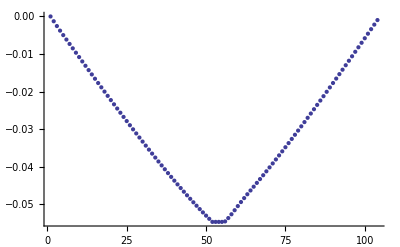

```mathematica
val=Table[ResultB[[i,1]],{i,Length[ResultB]}]
ListPlot[val]
ClearAll[val]
```

```mathematica
FromIJ[ResultIJ[[2,2]]]
FromIJ[ResultIJL[[2,2]]]
ToIJ[ListETotalB[[1]]]
ResultIJ[[2,4]]
ResultIJL[[2,4]]
```

{-0.000838619,-0.000217913}

{-0.000838619,-0.000217913}

{0.,0.,1}

{-0.26,0.0600444,1}

{-0.26,0.0600444,1}

{{0.,0.,1},{-0.0000255553,0.000392191,1},{-0.0000489052,0.000549126,1},{-0.000128836,0.000618811,1},{-0.00023899,0.000660876,1},{-0.000362129,0.000694147,1},{-0.000491461,0.000724602,1},{-0.000624616,0.00075422,1},{-0.000760818,0.000783683,1},{-0.000899849,0.000813232,1},{-0.00104169,0.000842959,1},{-0.0011864,0.000872899,1},{-0.00133407,0.000903068,1},{-0.00148481,0.000933474,1},{-0.00163871,0.000964124,1},{-0.00179591,0.000995021,1},{-0.00195653,0.00102617,1},{-0.00212071,0.00105758,1},{-0.00228858,0.00108925,1},{-0.0024603,0.00112119,1},{-0.00263604,0.0011534,1},{-0.00281594,0.00118588,1},{-0.0030002,0.00121865,1},{-0.003189,0.0012517,1},{-0.00338255,0.00128504,1},{-0.00358104,0.00131869,1},{-0.00378472,0.00135263,1},{-0.00399382,0.00138689,1},{-0.0042086,0.00142146,1},{-0.00442932,0.00145636,1},{-0.00465628,0.00149158,1},{-0.00488979,0.00152714,1},{-0.00513017,0.00156304,1},{-0.00537779,0.0015993,1},{-0.00563301,0.00163591,1},{-0.00589624,0.00167288,1},{-0.00616791,0.00171023,1},{-0.00644849,0.00174796,1},{-0.00673848,0.00178608,1},{-0.0070384,0.00182459,1},{-0.00734883,0.00186351,1},{-0.00767038,0.00190285,1},{-0.00800372,0.0019426,1},{-0.00834955,0.00198278,1},{-0.00870864,0.00202339,1},{-0.0090818,0.00206444,1},{-0.00946992,0.00210593,1},{-0.00987394,0.00214786,1},{-0.0102949,0.00219023,1},{-0.0107338,0.00223302,1},{-0.0111918,0.00227622,1},{-0.0116702,0.00231981,1},{-0.0116702,0.00231981,1},{-0.0103702,0.00156925,1},{-0.00907018,0.000818698,1},{-0.00789818,0.0000667578,1},{-0.00749002,0.000594102,-1},{-0.00719683,0.00113061,-1},{-0.00697471,0.00152265,-1},{-0.00677294,0.00177027,-1},{-0.00655188,0.00190065,-1},{-0.00629822,0.00195348,-1},{-0.00601883,0.00196183,-1},{-0.00572635,0.00194641,-1},{-0.00543116,0.00191867,-1},{-0.00513983,0.00188464,-1},{-0.00485597,0.00184749,-1},{-0.0045813,0.0018089,-1},{-0.00431649,0.00176975,-1},{-0.00406159,0.00173048,-1},{-0.00381641,0.00169136,-1},{-0.00358058,0.00165249,-1},{-0.00335368,0.00161394,-1},{-0.00313527,0.00157575,-1},{-0.00292494,0.00153793,-1},{-0.00272226,0.00150047,-1},{-0.00252685,0.00146338,-1},{-0.00233832,0.00142665,-1},{-0.00215634,0.00139028,-1},{-0.00198058,0.00135427,-1},{-0.00181071,0.0013186,-1},{-0.00164647,0.00128327,-1},{-0.00148757,0.00124828,-1},{-0.00133376,0.00121361,-1},{-0.0011848,0.00117927,-1},{-0.00104047,0.00114525,-1},{-0.000900546,0.00111153,-1},{-0.000764838,0.00107812,-1},{-0.000633156,0.00104501,-1},{-0.000505322,0.0010122,-1},{-0.000381169,0.000979674,-1},{-0.000260539,0.000947432,-1},{-0.000143283,0.00091547,-1},{-0.0000292613,0.000883781,-1},{0.0000816607,0.000852362,-1},{0.000189608,0.000821208,-1},{0.000294702,0.000790314,-1},{0.000397053,0.000759675,-1},{0.00049677,0.000729289,-1},{0.000593954,0.00069915,-1},{0.000688702,0.000669254,-1},{0.000781106,0.000639598,-1},{0.000871252,0.000610177,-1},{0.000959224,0.000580988,-1}}

{{0.,0.,1},{-0.00170369,0.0313752,1},{-0.00326035,0.0439301,1},{-0.00858908,0.0495049,1},{-0.0159327,0.05287,1},{-0.0241419,0.0555318,1},{-0.0327641,0.0579681,1},{-0.0416411,0.0603376,1},{-0.0507212,0.0626946,1},{-0.0599899,0.0650586,1},{-0.0694461,0.0674367,1},{-0.0790936,0.0698319,1},{-0.0889383,0.0722454,1},{-0.098987,0.0746779,1},{-0.109247,0.0771299,1},{-0.119727,0.0796017,1},{-0.130435,0.0820938,1},{-0.14138,0.0846064,1},{-0.152572,0.08714,1},{-0.16402,0.089695,1},{-0.175736,0.0922716,1},{-0.187729,0.0948704,1},{-0.200013,0.0974917,1},{-0.2126,0.100136,1},{-0.225503,0.102804,1},{-0.238736,0.105495,1},{-0.252315,0.108211,1},{-0.266255,0.110951,1},{-0.280573,0.113717,1},{-0.295288,0.116509,1},{-0.310419,0.119327,1},{-0.325986,0.122171,1},{-0.342012,0.125043,1},{-0.358519,0.127944,1},{-0.375534,0.130872,1},{-0.393083,0.13383,1},{-0.411194,0.136818,1},{-0.4299,0.139837,1},{-0.449232,0.142886,1},{-0.469227,0.145967,1},{-0.489922,0.149081,1},{-0.511359,0.152228,1},{-0.533581,0.155408,1},{-0.556637,0.158622,1},{-0.580576,0.161871,1},{-0.605454,0.165156,1},{-0.631328,0.168475,1},{-0.658262,0.171829,1},{-0.686324,0.175218,1},{-0.715584,0.178641,1},{-0.746119,0.182098,1},{-0.778012,0.185585,1},{-0.778012,0.185585,1},{-0.691346,0.12554,1},{-0.604679,0.0654958,1},{-0.526545,0.00534062,1},{-0.499334,0.0475282,1},{-0.479789,0.0904486,1},{-0.46498,0.121812,1},{-0.45153,0.141622,1},{-0.436792,0.152052,1},{-0.419881,0.156278,1},{-0.401256,0.156946,1},{-0.381757,0.155713,1},{-0.362077,0.153494,1},{-0.342655,0.150771,1},{-0.323731,0.1478,1},{-0.30542,0.144712,1},{-0.287766,0.14158,1},{-0.270773,0.138439,1},{-0.254427,0.135309,1},{-0.238705,0.132199,1},{-0.223578,0.129116,1},{-0.209018,0.12606,1},{-0.194996,0.123034,1},{-0.181484,0.120037,1},{-0.168456,0.11707,1},{-0.155888,0.114132,1},{-0.143756,0.111223,1},{-0.132038,0.108341,1},{-0.120714,0.105488,1},{-0.109765,0.102662,1},{-0.0991713,0.0998623,1},{-0.0889173,0.0970891,1},{-0.0789867,0.0943418,1},{-0.0693645,0.0916198,1},{-0.0600364,0.0889226,1},{-0.0509892,0.0862499,1},{-0.0422104,0.0836012,1},{-0.0336881,0.080976,1},{-0.0254112,0.0783739,1},{-0.0173693,0.0757946,1},{-0.00955223,0.0732376,1},{-0.00195075,0.0707025,1},{0.00544405,0.068189,1},{0.0126406,0.0656966,1},{0.0196468,0.0632251,1},{0.0264702,0.060774,1},{0.033118,0.0583431,1},{0.0395969,0.055932,1},{0.0459135,0.0535403,1},{0.0520737,0.0511678,1},{0.0580835,0.0488141,1},{0.0639483,0.046479,1}}

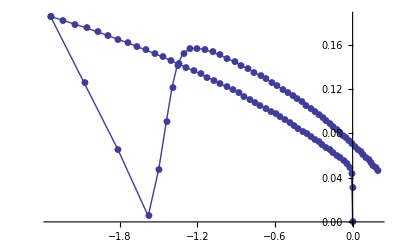

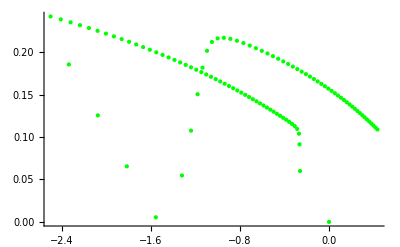

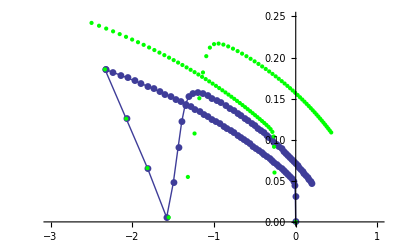

{{0,0,0},{0.00340737,0,0},{0.0065207,0,0},{0.0171782,0,0},{0.0318654,0,0},{0.0482839,0,0},{0.0655281,0,0},{0.0832822,0,0},{0.101442,0,0},{0.11998,0,0},{0.138892,0,0},{0.158187,0,0},{0.177877,0,0},{0.197974,0,0},{0.218495,0,0},{0.239455,0,0},{0.260871,0,0},{0.282761,0,0},{0.305144,0,0},{0.328041,0,0},{0.351471,0,0},{0.375459,0,0},{0.400027,0,0},{0.4252,0,0},{0.451006,0,0},{0.477473,0,0},{0.50463,0,0},{0.53251,0,0},{0.561147,0,0},{0.590576,0,0},{0.620838,0,0},{0.651972,0,0},{0.684023,0,0},{0.717038,0,0},{0.751068,0,0},{0.786165,0,0},{0.822388,0,0},{0.859799,0,0},{0.898464,0,0},{0.938453,0,0},{0.979844,0,0},{1.02272,0,0},{1.06716,0,0},{1.11327,0,0},{1.16115,0,0},{1.21091,0,0},{1.26266,0,0},{1.31652,0,0},{1.37265,0,0},{1.43117,0,0},{1.49224,0,0},{1.55602,0,0},{1.55602,0,0},{1.38269,0,0},{1.20936,0,0},{1.05309,0,0},{0.998669,0,2},{0.959578,0,2},{0.929961,0,2},{0.903059,0,2},{0.873584,0,2},{0.839762,0,2},{0.802511,0,2},{0.763514,0,2},{0.724154,0,2},{0.685311,0,2},{0.647463,0,2},{0.610841,0,2},{0.575532,0,2},{0.541546,0,2},{0.508855,0,2},{0.47741,0,2},{0.447157,0,2},{0.418036,0,2},{0.389992,0,2},{0.362968,0,2},{0.336913,0,2},{0.311776,0,2},{0.287512,0,2},{0.264077,0,2},{0.241429,0,2},{0.219529,0,2},{0.198343,0,2},{0.177835,0,2},{0.157973,0,2},{0.138729,0,2},{0.120073,0,2},{0.101978,0,2},{0.0844208,0,2},{0.0673762,0,2},{0.0508225,0,2},{0.0347385,0,2},{0.0191045,0,2},{0.0039015,0,2},{-0.0108881,0,2},{-0.0252811,0,2},{-0.0392935,0,2},{-0.0529404,0,2},{-0.066236,0,2},{-0.0791939,0,2},{-0.0918269,0,2},{-0.104147,0,2},{-0.116167,0,2},{-0.127897,0,2}}

{-0.07,-0.0392401,-0.0272456,-0.023576,-0.0228031,-0.0229942,-0.023504,-0.0241149,-0.0247519,-0.0253883,-0.0260141,-0.0266254,-0.0272203,-0.0277978,-0.0283571,-0.0288975,-0.0294185,-0.0299193,-0.0303991,-0.0308574,-0.0312934,-0.0317062,-0.032095,-0.0324589,-0.032797,-0.0331084,-0.0333919,-0.0336464,-0.0338708,-0.0340639,-0.0342244,-0.0343508,-0.0344417,-0.0344955,-0.0345107,-0.0344853,-0.0344177,-0.0343057,-0.0341474,-0.0339405,-0.0336827,-0.0333716,-0.0330046,-0.0325791,-0.0320923,-0.0315414,-0.0309235,-0.0302358,-0.0294755,-0.02864,-0.027727,-0.0267344,-0.0267344,-0.0796084,-0.131118,-0.182195,-0.136496,-0.0909316,-0.0574952,-0.0357481,-0.0231343,-0.0163211,-0.0127007,-0.0107219,-0.00956966,-0.00883113,-0.00829797,-0.00786467,-0.00747808,-0.00711184,-0.0067534,-0.00639729,-0.00604165,-0.00568635,-0.00533214,-0.00498007,-0.00463134,-0.00428709,-0.00394844,-0.00361636,-0.00329175,-0.00297541,-0.00266804,-0.00237023,-0.00208252,-0.00180535,-0.00153911,-0.00128412,-0.00104063,-0.000808879,-0.000589019,-0.000381183,-0.000185463,-1.9171×10^-6,0.000169424,0.000328556,0.0004755,0.000610294,0.000732998,0.000843687,0.000942449,0.00102939,0.00110461,0.00116824}

```mathematica
DeformElastB=Table[ToIJ[ListETotalB[[i]]-FromIJ[ResultIJ[[i,2]]]],{i,1,Length[ListETotalB]}]
SigElastIJB=Table[{K DeformElastB[[i,1]],2 G DeformElastB[[i,2]],ResultIJ[[i,2,3]]}/.exemple,{i,1,Length[ListETotalB]}]
SigElastIJB2=Table[{3K DeformElastB[[i,1]],2 G DeformElastB[[i,2]]}/.exemple,{i,1,Length[ListETotalB]}];
SigTrialIJB=Table[{ResultIJ[[i,4,1]],ResultIJ[[i,4,2]]},{i,Length[ResultIJ]}];
glB=ListPlot[SigElastIJB2,PlotJoined->True,PlotMarkers->Automatic]
gl2B=ListPlot[SigTrialIJB,PlotStyle->{Green}]
Show[glB,gl2B,PlotRange->{{-3,1},{0,0.25}}]
Diff=Table[SigElastIJB[[i]]-ResultIJ[[i,3]],{i,1,Length[ListETotalB]}]//Chop
Table[Function1[ResultIJ[[i,3,1]],ResultIJ[[i,3,2]]],{i,1,Length[ListETotalB]}]
```

{{0.,0},{-0.0013,-0.0379327},{-0.0026,-0.0539865},{-0.0039,-0.0657524},{-0.0052,-0.0769818},{-0.0065,-0.0882645},{-0.0078,-0.0996999},{-0.0091,-0.111313},{-0.0104,-0.123115},{-0.0117,-0.135113},{-0.013,-0.147315},{-0.0143,-0.159729},{-0.0156,-0.17236},{-0.0169,-0.185218},{-0.0182,-0.198309},{-0.0195,-0.211643},{-0.0208,-0.225229},{-0.0221,-0.239076},{-0.0234,-0.253193},{-0.0247,-0.267591},{-0.026,-0.282282},{-0.0273,-0.297276},{-0.0286,-0.312587},{-0.0299,-0.328227},{-0.0312,-0.34421},{-0.0325,-0.360551},{-0.0338,-0.377266},{-0.0351,-0.39437},{-0.0364,-0.411882},{-0.0377,-0.429821},{-0.039,-0.448205},{-0.0403,-0.467057},{-0.0416,-0.486399},{-0.0429,-0.506256},{-0.0442,-0.526652},{-0.0455,-0.547617},{-0.0468,-0.569178},{-0.0481,-0.591369},{-0.0494,-0.614222},{-0.0507,-0.637775},{-0.052,-0.662066},{-0.0533,-0.687136},{-0.0546,-0.713031},{-0.0559,-0.739798},{-0.0572,-0.767489},{-0.0585,-0.796159},{-0.0598,-0.825866},{-0.0611,-0.856673},{-0.0624,-0.888648},{-0.0637,-0.921861},{-0.065,-0.956388},{-0.0663,-0.992307},{-0.0663,-0.992307},{-0.065,-0.836307},{-0.0637,-0.680307},{-0.0624,-0.532712},{-0.0611,-0.444454},{-0.0598,-0.375348},{-0.0585,-0.324324},{-0.0572,-0.287999},{-0.0559,-0.261218},{-0.0546,-0.239427},{-0.0533,-0.22003},{-0.052,-0.201955},{-0.0507,-0.184838},{-0.0494,-0.16856},{-0.0481,-0.153067},{-0.0468,-0.138321},{-0.0455,-0.124284},{-0.0442,-0.110918},{-0.0429,-0.0981866},{-0.0416,-0.0860547},{-0.0403,-0.0744886},{-0.039,-0.0634564},{-0.0377,-0.0529285},{-0.0364,-0.0428768},{-0.0351,-0.0332754},{-0.0338,-0.0240999},{-0.0325,-0.0153273},{-0.0312,-0.00693647},{-0.0299,0.00109272},{-0.0286,0.00877894},{-0.0273,0.0161397},{-0.026,0.0231915},{-0.0247,0.0299498},{-0.0234,0.036429},{-0.0221,0.0426426},{-0.0208,0.0486036},{-0.0195,0.0543239},{-0.0182,0.0598149},{-0.0169,0.0650872},{-0.0156,0.0701508},{-0.0143,0.0750152},{-0.013,0.0796894},{-0.0117,0.0841819},{-0.0104,0.0885005},{-0.0091,0.0926528},{-0.0078,0.096646},{-0.0065,0.100487},{-0.0052,0.104182},{-0.0039,0.107737},{-0.0026,0.111157},{-0.0013,0.114449},{0.,0.117618}}

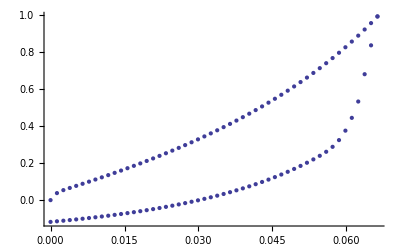

-Graphics-

```mathematica
a=Table[{ListETotalB[[i,1]],ResultB[[i,3,1]]},{i,1,Length[ListETotalB]}]
ga=ListPlot[-a]
Show[ga]
Clear[a,ga]
```

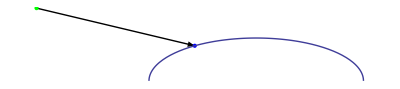

```mathematica
ShowPointB[ResultIJ_,i_]:=Block[{frompoint,topoint,arrow,dot1,dot2,ellips},
frompoint={ResultIJ[[i,4,1]],ResultIJ[[i,4,2]]};
topoint={ResultIJ[[i,3,1]],ResultIJ[[i,3,2]]};
arrow=Graphics[{Arrowheads[0.02],Arrow[{frompoint,topoint}]}];
dot1=Graphics[{PointSize[Large],Green,Point[frompoint]}];
dot2=Graphics[{PointSize[Large],Blue,Point[topoint]}];
ellips=Ag[LFunction[ResultB[[i,1]]]];
{arrow,dot1,dot2,ellips}
]
Show[ShowPointB[ResultIJ,5]]
```

```mathematica
Animate[Show[ShowPointB[ResultIJ,i],PlotRange->{{-3,2},{-0.1,0.4}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
Animate[Show[glB,bg,gl2B,ShowPoint[ResultIJ,i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJ],1},AnimationRunning->False]
```

```mathematica
TableShowPointB=Table[Show[glB,bg,gl2B,ShowPoint[ResultIJ,i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJ]}];
stringB=NotebookDirectory[];
FileAnimationB=string<>"AnimationB.gif";
Export[FileAnimationB,TableShowPointB]
```

/Users/nathanshauer/Dropbox/Projeto_LabMec_2011_14/Plasticidade/Aprendizado/AnimationB.gif

```mathematica
a=Derivatives[Result[[1,3]],Result[[2,3]]-Result[[1,3]],Result[[1,1]]];
{{a[[1,1]]Sqrt[3],a[[1,2]]},{a[[2,1]]Sqrt[3],a[[2,2]]},a[[3]]}
{ListETotal[[2]],Result[[2,2]],Result[[2,1]]}
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.00191967,0.0157458}

dlval = 17.0081

B lval = 0.08914

- C B E^(B lval) = -0.131844

dfval = -2.24242

one = 255.675

two = 84.2732

three = 0.

four = 0.

df2depsp = 339.949

epspponto = -0.00014703

trN2 = -45.0976

gammaponto = 3.26026×10^-6

deformPlast = {-0.0000848878,0.}

ST = {0,1}

deformElast = {-0.0000166248,0.000196822}

{{-0.000175825,0.000196822},{-0.00014703,0.},-0.00014703}

{{-0.000325,0.000187639},{-0.000275126,0.0000484644},-0.000275126}

```mathematica
ElastoPlastic[Result[[1,1]],Result[[1,2]],ListETotal[[2]]]
```

ETotal = {-0.000325,0.000187639}

SigI1xJ2 = {-0.0216667,0.0150111}

valf2 = 0.431788

subit {I1T→-0.0216667,J2T→0.0150111}

θ = -π

θ = -(19 π)/20

θ = -(9 π)/10

θ = -(17 π)/20

θ = -(4 π)/5

θ = -(3 π)/4

θ = -(7 π)/10

θ = -(13 π)/20

θ = -(3 π)/5

θ = -(11 π)/20

θ = -π/2

θ = -(9 π)/20

θ = -(2 π)/5

θ = -(7 π)/20

θ = -(3 π)/10

θ = -π/4

θ = -π/5

θ = -(3 π)/20

θ = -π/10

θ = -π/20

θ = 0

θ = π/20

θ = π/10

θ = (3 π)/20

θ = π/5

θ = π/4

θ = (3 π)/10

θ = (7 π)/20

θ = (2 π)/5

θ = (9 π)/20

θ = π/2

θ = (11 π)/20

θ = (3 π)/5

θ = (13 π)/20

θ = (7 π)/10

θ = (3 π)/4

θ = (4 π)/5

θ = (17 π)/20

θ = (9 π)/10

θ = (19 π)/20

θ = π

restheta = {5.67729,5.34003,5.12872,4.9867,4.87787,4.78283,4.69152,4.5989,4.5027,4.4021,4.29704,4.18782,4.07487,3.9587,3.83975,3.71847,3.59526,3.47045,3.34437,3.21729,3.08947,2.96115,3.45065,3.57936,3.70797,3.83632,3.96425,4.09163,4.21839,4.34455,4.47028,4.59604,4.72284,4.85265,4.98938,5.14073,5.32211,5.56417,5.91817,0.122311,0.605891}

θ = (19 π)/20

θ = (19 π)/20

residue = {0.122311,0.00034957}

tangent = {{3.32067,-242.53},{-0.000312192,1.33818}}

delu = {0.0568818,0.000274499}

θ = 2.92763

delepsp = -0.000274499

θ = 2.92763

residue = {-0.0229419,3.22682×10^-6}

tangent = {{4.02657,-202.504},{-0.000428652,1.33871}}

delu = {-0.00566767,5.95617×10^-7}

θ = 2.9333

delepsp = -0.000275094

θ = 2.9333

residue = {0.0000914666,3.16371×10^-8}

tangent = {{4.05591,-225.014},{-0.000417475,1.33881}}

delu = {0.0000242825,3.12026×10^-8}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {-1.41228×10^-9,5.93007×10^-13}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {-3.29334×10^-10,3.40229×10^-13}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,1.6263×10^-19}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {6.85528×10^-18,1.23612×10^-19}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,5.42101×10^-20}

Function2 = 2.22045×10^-16

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
{K,2G}/.exemple
{ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple
(%-Result[[2,3]])/.exemple
{%[[1]]/K,%[[2]]/(2G)}/.exemple
```

{66.6667,80}

{-0.216667,0.150111}

{-0.179007,0.117562}

{-0.0026851,0.00146953}

```mathematica
Result[[2]]
```

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
epsp=Result[[2,1]]
theta=2.5604883056356527;
l=LFunction[epsp];
fl=F[l]/.exemple;
i1theta=l+fl R Cos[theta]/.exemple;
i1=Result[[2,3,1]];
i1-i1theta;
sqj2=Result[[2,3,2]];
sqj2theta=fl Sin[theta];
sqj2theta-sqj2;
(l-i1)^2 /(fl R)^2 + sqj2^2/fl^2 -1/.exemple;
gfv1=2√3(i1-l)/(fl R)^2/.exemple;
√3 gfv1;
gfv2=√2 sqj2/fl^2;
sqj2/fl;
ep=Result[[2,2]];
ArcTan[ep[[1]],ep[[2]]]
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple
ArcTan[epprop[[1]],epprop[[2]]]
TmTt={K epprop[[1]],2G epprop[[2]]}/.exemple
sigtrial={ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple;
sigma=Result[[2,3]]
difsigma=(sigtrial-sigma)/.exemple;
ArcTan[difsigma[[1]],difsigma[[2]]]
ep-{difsigma[[1]]/K,difsigma[[2]]/(2G)}/.exemple
ArcTan[TmTt[[1]],TmTt[[2]]]
ArcTan[2 G R difsigma[[1]],3K difsigma[[2]]]/.exemple
theta
difsigma

Print[" delta gamma ",δγ2=epsp/epprop[[1]]]
Tepprop={K epprop[[1]],2G epprop[[2]]}/.exemple;
toto=Tepprop δγ2
ArcTan[difsigma[[1]],difsigma[[2]]]
ArcTan[toto[[1]],toto[[2]]]
δγ2 epprop-ep


Print["Checking stress functions"];
sigma
sqj2
l
fl
Print["gradf ",{epprop[[1]]/Sqrt[3],epprop[[2]]/Sqrt[2]}]
{sigma[[1]]/Sqrt[3],sigma[[2]]Sqrt[2]}

DLFunction[epsp]
B l/.exemple
dF[l]/.exemple
DLFunction[epsp]dF[l]/.exemple
a=DLFunction[epsp](2(l-i1))/(fl R)^2/.exemple
b=DLFunction[epsp](-(2(l-i1)^2)/(fl^3 R^2)dF[l])/.exemple
c=DLFunction[epsp](-(2sigma[[2]]^2)/fl^3 dF[l])/.exemple
Print["four ",DLFunction[epsp](-(2sigma[[2]]^2)/1 dF[l])/.exemple]
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,a=epponto=-gradFT/dfedep]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]

epsp=0;
i1=0;
sqj2=0;
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple;
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,b=epponto=-gradFT/dfedep]
Print["epponto medio ",(a+b)/2]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]


ClearAll[l,fl,i1,sqj2,gfv1,gfv2,epsp,theta,i1theta,sqj2theta,ep,epprop,TmTt,sigtrial,sigma,difsigma,Tepprop,toto,δγ2,dfedep,gradFT,epponto,a,b,c,gammaponto]
```

-0.000275126

2.96723

{-43.6165,7.68321}

2.96723

{-2907.77,614.657}

{-0.00332496,0.011134}

2.93327

{0.,0.}

2.93327

2.93327

2.56049

{-0.0183417,0.00387715}

delta gamma 6.30783×10^-6

{-0.0183417,0.00387715}

2.93327

2.93327

{5.42101×10^-20,-4.06576×10^-20}

Checking stress functions

{-0.00332496,0.011134}

0.011134

0.128354

0.0538354

gradf {-25.182,5.43285}

{-0.00191967,0.0157458}

17.0926

0.0859971

-0.13143

-2.24649

248.507

79.888

3.56967

four 0.000556972

331.965

0.133886

epponto -0.000403313

TrN2 -43.6165

gammaponto 9.2468×10^-6

316.564

0.0471204

epponto -0.00014885

epponto medio -0.000276081

TrN2 -42.5151

gammaponto 3.5011×10^-6

```mathematica
K
```

K